# Tight Binding Model for Studying the Effect of Spin-Orbit Coupling in Multi-layers in the Frame of Linear Response theory

```mathematica
Needs["GreenSlab`"];
```

Welcome to GreenSlab.
		G | RGBColor[0, 1, 1] | 0 | 0 | 0 | 0 | 0 | 0 | 0
RGBColor[0, 1, 1] | R | RGBColor[1, Rational[1, 2], Rational[1, 2]] | 0 | 0 | 0 | 0 | 0 | 0
0 | RGBColor[1, Rational[1, 2], Rational[1, 2]] | E | RGBColor[0, 1, 0] | 0 | 0 | 0 | 0 | 0
0 | 0 | RGBColor[0, 1, 0] | E | RGBColor[0, 1, 0] | 0 | 0 | 0 | 0
0 | 0 | 0 | RGBColor[0, 1, 0] | N | RGBColor[0, Rational[2, 3], Rational[2, 3]] | RGBColor[0, Rational[2, 3], Rational[2, 3]] | 0 | 0
0 | 0 | 0 | 0 | RGBColor[0, Rational[2, 3], Rational[2, 3]] | S | RGBColor[0, 0, 1] | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0]
0 | 0 | 0 | 0 | RGBColor[0, Rational[2, 3], Rational[2, 3]] | RGBColor[0, 0, 1] | L | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0]
0 | 0 | 0 | 0 | 0 | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0] | A | RGBColor[0, 0, 1]
0 | 0 | 0 | 0 | 0 | RGBColor[1, 0.5, 0] | RGBColor[1, 0.5, 0] | RGBColor[0, 0, 1] | B

The package will help you to build a slab Hamiltonian
for a given number of layers.
You can construct the retarded or advanced Greens function
and use it in Linear Response Theory.
It can also calculate normal band structure and band structure with 
a weight corresponding to an operator.

■
While calling the the inbuilt functions use them in a definition rather than
in a function. For example use
		 f[kx_]=Combine[Cos[kx],-Cos[kx],1]
not	  f[kx_]:=Combine[Cos[kx],-Cos[kx],1]

■
Gr and Ga involves Inverse. For large Hamiltonians (n>4) either use Gr,Ga in functions

for example 	 a[x_]:=Gr[H[x]]-Ga[H[x]]

or use a numerical matrix for H. Otherwise it may take ages to evaluate.

■
Type Info[GreenSlab] to see all available functions and info[function_name]
to get information about a particular function.

Sumit Ghosh 18-07-2018 V1.0 (sumit.ghosh@kaust.edu.sa)

## Parameters

```mathematica
Clear[VsF,VdF,VpF,VsN,VdN,VpN,VsFN,VdFN,VpFN,a0,ExyF,ExzF,EyzF,ExyN,ExzN,EyzN,JxyF,JxzF,JyzF,V0n,Vn,Vf,J,xi,eta,th,fi,G,hbar,ehbar,n,Nn,Ef,L,ch]
nbF =0;
nbN= 9;
ch[i_]:=xi;
(*Slater-Koster 2-center parameters,  Orthogonal, 1rst neighbor and 2nd neighbor Handbook of the Band Structure of Elemental Solids, we use iron and tungsten as they are bcc*)
(*maybe not useful as we implement magnetization by hand*)

(*
VsF1up= -0.04541*13.6;(*Fe*) (*-0.0388*13.6Co up*)
VpF1up= 0.02714*13.6;(*Fe*) (*0.02387*13.6Co up*)
VdF1up= -0.00260*13.6;(*Fe*) (*-0.00384*13.6Co up*)
VsF1down= -0.05266*13.6 ;(*Fe*) (*-0.04403*13.6Co up*)
VpF1down=  0.03276*13.6;(*Fe*) (*0.02763*13.6Co up*)
VdF1down=-0.00286*13.6 ;(*Fe*) (*-0.00442*13.6Co up*)

VsF2up=-0.02713*13.6;(*Fe*) (*-0.00669*13.6 Co up*)
VpF2up=0.00589*13.6;(*Fe*) (*0.00167*13.6 Co up*)
VdF2up=0.00060*13.6;(*Fe*) (*0.00023*13.6 Co up*)
VsF2down=-0.03396*13.6;(*Fe*) (*-0.00793*13.6 Co down*)
VpF2down=0.00581*13.6;(*Fe*) (*0.00198*13.6 Co down*)
VdF2down=0.00114*13.6;(*Fe*) (*0.00026*13.6 Co down*)
*)
(*here we write our parameters*)
VsF1= -0.04541*13.6;(*Fe*) (*-0.0388*13.6Co up*)
VpF1= 0.02714*13.6;(*Fe*) (*0.02387*13.6Co up*)
VdF1= -0.00260*13.6;(*Fe*) (*-0.00384*13.6Co up*)

VsF2=-0.02713*13.6;(*Fe*) (*-0.00669*13.6 Co up*)
VpF2=0.00589*13.6;(*Fe*) (*0.00167*13.6 Co up*)
VdF2=0.00060*13.6;(*Fe*) (*0.00023*13.6 Co up*)

VsN1= -0.11837*13.6;(*W*) (* -0.06856*13.6 Pt fcc*)
VpN1= 0.05194*13.6; (*W*) (* 0.03528*13.6 Pt fcc*)
VdN1= 0.00248*13.6;(*W*) (* -0.00588*13.6 Pt fcc*)

VsN2= -0.07313*13.6;(*W*) 
VpN2= -0.01264*13.6; (*W*) 
VdN2= 0.00908*13.6;(*W*) 

VsFN1=-(0.04541+0.11837)*13.6/2; 
VpFN1=( 0.02714+0.05194)*13.6/2;
VdFN1=(-0.00260+0.00248)*13.6/2;

VsFN2=-(0.02713+0.07313)*13.6/2; 
VpFN2=( 0.00589 -0.01264)*13.6/2;
VdFN2=(0.00060+0.00908)*13.6/2;
(* -13.6 eV is the binding Energy of the elecron of the Hydrogen atom *)
a0=0.316*10^-9;(*m*)
ExyF=E0+t2gF;(*t2gFUp=0.64840*13.6,t2gFDn=0.78456*13.6*)
ExzF=E0+t2gF;(*t2gFUp=0.64840*13.6,t2gFDn=0.78456*13.6*)
EyzF=E0+t2gF;(*t2gFUp=0.64840*13.6,t2gFDn=0.78456*13.6*)
Ex2y2F=E0+egF;(*egFUp=0.62960*13.6, egFDn=0.75661*13.6*)
Ez2F=E0+egF;(*egFUp=0.62960*13.6, egFDn=0.75661*13.6*)
ExyN=t2gN;(*t2gN=0.96813*13.6*)
ExzN=t2gN;(*t2gN=0.96813*13.6*)
EyzN=t2gN;(*t2gN=0.96813*13.6*)
Ex2y2N=egN;(*egN=0.85720*13.6*)
Ez2N=egN;(*egN=0.85720*13.6*)
JxyF=Jt2g;
JxzF=Jt2g;
JyzF=Jt2g;
Jx2y2F=Jeg;
Jz2F=Jeg;
t2gN=0.96813*13.6;
egN=0.85720*13.6;
E0=4.0;
t2gF=(0.64840*13.6+0.78456*13.6)/2;
egF=(0.62960*13.6+0.75661*13.6)/2;
Jt2g=(0.64840*13.6-0.78456*13.6);
Jeg=Jt2g;
(*Jeg=(0.62960*13.6-0.75661*13.6);*)
xi=0.014*13.6;(*0.36 W*) (*0.4 Pt*) (* 0.065 Co*)(*in Solid State Physics by Aurelien*)
eta=Pi/4;
th=0;
fi=0;
hbar=6.58*10^-16;(*eV.s*)
ehbar=6.58*10^-16*1.6*10^-19;
Ef=14.0; (* eV /real Fermi energy of Tungsten: 11eV*)
G=0.05;
muB=5.788*10^-5;(*eV/Oe*)
Vmag=muB*ee/(Ms*L*a0);(*m^2 - see below*)
ee=1.6*10^-19;
Ms=800*10^3;(*A/m*)
L=3;
n=100;
```

Some standard values: Ef=1.5, V0=-1, J=1; then play around; typical effective magnetic volume is \muB/(Msd)=1.157x10^-20 m^2, with Ms=800emu/cc, d=1nm
Then, the test formula is (J/muB)*(muB/Msd)*IntISGE/(Cxx/d)*10^12...this gives the torque efficiency in Oe/(10^8A/cm2).
The effective spin Hall conductance reads J*IntISGE*(2*e/hbar)*10^-4...this gives the spin Hall conductivity in (\hbar/2e) 10^4 Ohm^-1.m^-1

Note: looks like n=300 is the best, but n=200 is ok; n=100 is too small

## Hopping parameters according to Slater Koster

```mathematica
gxyF[kx_,ky_]:=(3*VsF2+VdF2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gxzF[kx_,ky_]:=(VpF2+VdF2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gyzF[kx_,ky_]:=(VpF2+VdF2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gx2y2F[kx_,ky_]:= 2*VpF2 *(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gz2F[kx_,ky_]:=  (VsF2+3*VdF2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gxyN[kx_,ky_]:=(3*VsN2+VdN2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gxzN[kx_,ky_]:=(VpN2+VdN2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gyzN[kx_,ky_]:=(VpN2+VdN2)*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gx2y2N[kx_,ky_]:= 2*VpN2 *(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);
gz2N[kx_,ky_]:=  (VsN2+3*VdN2)/2*(Cos[(kx+ky)*a0/2]+Cos[(kx-ky)*a0/2]);

TxyFxzF[kx_,ky_]:=0;
TxyFyzF[kx_,ky_]:=0;
TxzFyzF[kx_,ky_]:=(VpF2-VdF2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TxyFx2y2F[kx_,ky_]:=0;
TyzFx2y2F[kx_,ky_]:=0;
TxzFx2y2F[kx_,ky_]:=0;
Tz2Fx2y2F[kx_,ky_]:=0;
TxyFz2F[kx_,ky_]:=-Sqrt[3]/2*(VsF2-VdF2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TyzFz2F[kx_,ky_]:=0;
TxzFz2F[kx_,ky_]:=0;

TxyNxzN[kx_,ky_]:=0;
TxyNyzN[kx_,ky_]:=0;
TxzNyzN[kx_,ky_]:=(VpN2-VdN2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TxyNx2y2N[kx_,ky_]:=0;
TyzNx2y2N[kx_,ky_]:=0;
TxzNx2y2N[kx_,ky_]:=0;
Tz2Nx2y2N[kx_,ky_]:=0;
TxyNz2N[kx_,ky_]:=-Sqrt[3]/2*(VsN2-VdN2)*(Cos[(kx+ky)*a0/2]-Cos[(kx-ky)*a0/2]);
TyzNz2N[kx_,ky_]:=0;
TxzNz2N[kx_,ky_]:=0;

TxyFxyN[kx_,ky_]:=2*(VpFN1*Cos[eta]^2+VdFN1*Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
TyzFyzN[kx_,ky_]:=2*(VpFN1*Sin[eta]^2+VdFN1*Cos[eta]^2)*Cos[kx*a0/2]+2*((3*VsFN1+VdFN1-4*VpFN1)*Sin[eta]^2*Cos[eta]^2+VpFN1)*Cos[ky*a0/2];
TxzFxzN[kx_,ky_]:=2*(VpFN1*Sin[eta]^2+VdFN1*Cos[eta]^2)*Cos[ky*a0/2]+2*((3*VsFN1+VdFN1-4*VpFN1)*Sin[eta]^2*Cos[eta]^2+VpFN1)*Cos[kx*a0/2];
TxzFyzN[kx_,ky_]:=0;
TyzFxzN[kx_,ky_]:=0;
TxyFxzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[ky*a0/2];
TxyFyzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[kx*a0/2];
TxzFxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[ky*a0/2];
TyzFxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpFN1-VdFN1)*Sin[kx*a0/2];
TxyFx2y2N[kx_,ky_]:=0;
TyzFx2y2N[kx_,ky_]:=I/4* (-3 VdFN1+3 VsFN1+(VdFN1-4 VpFN1+3 VsFN1) Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2];
TxzFx2y2N[kx_,ky_]:=-I/4* (-3 VdFN1+3 VsFN1+(VdFN1-4 VpFN1+3 VsFN1) Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2];
Tz2Fx2y2N[kx_,ky_]:= -1/2 *√3 Cos[eta]^2 *(-VdFN1+VsFN1 Cos[eta]^2-(VdFN1-4 VpFN1+2 VsFN1) Sin[eta]^2)*Cos[kx*a0/2]+1/4* √3 Cos[eta]^2 (-3 VdFN1+4 VpFN1-VsFN1+(VdFN1-4 VpFN1+3 VsFN1) Cos[2 eta])*Cos[ky*a0/2];
Tx2y2Fx2y2N[kx_,ky_]:= (3/2 VsFN1 Cos[eta]^4+(1/8) VdFN1 (-3+Cos[2 eta])^2+2VpFN1 Cos[eta]^2  Sin[eta]^2)* (Cos[kx*a0/2]+Cos[ky*a0/2])  ;
TxyFz2N[kx_,ky_]:= 0;
TyzFz2N[kx_,ky_]:= I/4*Sqrt[3]* (VdFN1-VsFN1+(VdFN1-4 VpFN1+3 VsFN1) *Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2] ;
TxzFz2N[kx_,ky_]:= I/4*Sqrt[3]*(VdFN1-VsFN1+(VdFN1-4 VpFN1+3 VsFN1)* Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2] ;
Tz2Fz2N[kx_,ky_]:=(3/2 VdFN1 Cos[eta]^4+1/8 VsFN1 (1-3 Cos[2 eta])^2+6 VpFN1 Cos[eta]^2 Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);

zTxyNxyN[kx_,ky_]:=2*(VpN1*Cos[eta]^2+VdN1*Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
zTyzNyzN[kx_,ky_]:=2*(VpN1*Sin[eta]^2+VdN1*Cos[eta]^2)*Cos[kx*a0/2]+2*((3*VsN1+VdN1-4*VpN1)*Sin[eta]^2*Cos[eta]^2+VpN1)*Cos[ky*a0/2];
zTxzNxzN[kx_,ky_]:=2*(VpN1*Sin[eta]^2+VdN1*Cos[eta]^2)*Cos[ky*a0/2]+2*((3*VsN1+VdN1-4*VpN1)*Sin[eta]^2*Cos[eta]^2+VpN1)*Cos[kx*a0/2];
zTxzNyzN[kx_,ky_]:=0;
zTyzNxzN[kx_,ky_]:=0;
zTxyNxzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[ky*a0/2];
zTxyNyzN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[kx*a0/2];
zTxzNxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[ky*a0/2];
zTyzNxyN[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpN1-VdN1)*Sin[kx*a0/2];
zTxyNx2y2N[kx_,ky_]:=0;
zTyzNx2y2N[kx_,ky_]:=I/4* (-3 VdN1+3 VsN1+(VdN1-4 VpN1+3 VsN1) Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2];
zTxzNx2y2N[kx_,ky_]:=-I/4* (-3 VdN1+3 VsN1+(VdN1-4 VpN1+3 VsN1) Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2];
zTz2Nx2y2N[kx_,ky_]:= -1/2 *√3 Cos[eta]^2 *(-VdN1+VsN1 Cos[eta]^2-(VdN1-4 VpN1+2 VsN1)* Sin[eta]^2)*Cos[kx*a0/2]+1/4* √3 Cos[eta]^2 (-3 VdN1+4 VpN1-VsN1+(VdN1-4 VpN1+3 VsN1)*Cos[2 eta])*Cos[ky*a0/2];
zTx2y2Nx2y2N[kx_,ky_]:=(3/2 VsN1 Cos[eta]^4+(1/8) VdN1 (-3+Cos[2 eta])^2+2VpN1 Cos[eta]^2  Sin[eta]^2)* (Cos[kx*a0/2]+Cos[ky*a0/2])  ;
zTxyNz2N[kx_,ky_]:= 0;
zTyzNz2N[kx_,ky_]:= I/4*Sqrt[3]* (VdN1-VsN1+(VdN1-4 VpN1+3 VsN1) *Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2] ;
zTxzNz2N[kx_,ky_]:= I/4*Sqrt[3]*(VdN1-VsN1+(VdN1-4 VpN1+3 VsN1)* Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2] ;
zTz2Nz2N[kx_,ky_]:=(3/2 VdN1 Cos[eta]^4+1/8 VsN1 (1-3 Cos[2 eta])^2+6 VpN1 Cos[eta]^2 Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);

zTxyFxyF[kx_,ky_]:=2*(VpF1*Cos[eta]^2+VdF1*Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
zTyzFyzF[kx_,ky_]:=2*(VpF1*Sin[eta]^2+VdF1*Cos[eta]^2)*Cos[kx*a0/2]+2*((3*VsF1+VdF1-4*VpF1)*Sin[eta]^2*Cos[eta]^2+VpF1)*Cos[ky*a0/2];
zTxzFxzF[kx_,ky_]:=2*(VpF1*Sin[eta]^2+VdF1*Cos[eta]^2)*Cos[ky*a0/2]+2*((3*VsF1+VdF1-4*VpF1)*Sin[eta]^2*Cos[eta]^2+VpF1)*Cos[kx*a0/2];
zTxzFyzF[kx_,ky_]:=0;
zTyzFxzF[kx_,ky_]:=0;
zTxyFxzF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[ky*a0/2];
zTxyFyzF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[kx*a0/2];
zTxzFxyF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[ky*a0/2];
zTyzFxyF[kx_,ky_]:=-2*I*Sin[eta]*Cos[eta]*(VpF1-VdF1)*Sin[kx*a0/2];
zTxyFx2y2F[kx_,ky_]:=0;
zTyzFx2y2F[kx_,ky_]:=I/4* (-3 VdF1+3 VsF1+(VdF1-4 VpF1+3 VsF1) Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2];
zTxzFx2y2F[kx_,ky_]:=-I/4* (-3 VdF1+3 VsF1+(VdF1-4 VpF1+3 VsF1) Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2];
zTz2Fx2y2F[kx_,ky_]:= -1/2 *√3 Cos[eta]^2 *(-VdF1+VsF1 Cos[eta]^2-(VdF1-4 VpF1+2 VsF1) Sin[eta]^2)*Cos[kx*a0/2]+1/4* √3 Cos[eta]^2 (-3 VdF1+4 VpF1-VsF1+(VdF1-4 VpF1+3 VsF1) Cos[2 eta])*Cos[ky*a0/2];
zTx2y2Fx2y2F[kx_,ky_]:=(3/2 VsF1 Cos[eta]^4+(1/8) VdF1 (-3+Cos[2 eta])^2+2VpF1 Cos[eta]^2  Sin[eta]^2)* (Cos[kx*a0/2]+Cos[ky*a0/2])  ;
zTxyFz2F[kx_,ky_]:= 0;
zTyzFz2F[kx_,ky_]:= I/4*Sqrt[3]* (VdF1-VsF1+(VdF1-4 VpF1+3 VsF1) *Cos[2 eta]) *Sin[2 eta]*Sin[ky*a0/2] ;
zTxzFz2F[kx_,ky_]:= I/4*Sqrt[3]*(VdF1-VsF1+(VdF1-4 VpF1+3 VsF1)* Cos[2 eta]) *Sin[2 eta]*Sin[kx*a0/2] ;
zTz2Fz2F[kx_,ky_]:=(3/2 VdF1 Cos[eta]^4+1/8 VsF1 (1-3 Cos[2 eta])^2+6 VpF1 Cos[eta]^2 Sin[eta]^2)*(Cos[kx*a0/2]+Cos[ky*a0/2]);
```

## Single Multilayer Hamiltonian

```mathematica
MF[kx_,ky_]:={{ExyF+JxyF/2*Cos[th]+gxyF[kx,ky],JxyF/2*Exp[-I*fi]*Sin[th],TxyFxzF[kx,ky],0,TxyFyzF[kx,ky],0,TxyFz2F[kx,ky],0,TxyFx2y2F[kx,ky],0},{JxyF/2*Exp[I*fi]*Sin[th],ExyF-JxyF/2*Cos[th]+gxyF[kx,ky],0,TxyFxzF[kx,ky],0,TxyFyzF[kx,ky],0,TxyFz2F[kx,ky],0,TxyFx2y2F[kx,ky]},{TxyFxzF[kx,ky],0,ExzF+JxzF/2*Cos[th]+gxzF[kx,ky],JxzF/2*Exp[-I*fi]*Sin[th],TxzFyzF[kx,ky],0,TxzFz2F[kx,ky],0,TxzFx2y2F[kx,ky],0},{0,TxyFxzF[kx,ky],JxzF/2*Exp[I*fi]*Sin[th],ExzF-JxzF/2*Cos[th]+gxzF[kx,ky],0,TxzFyzF[kx,ky],0,TxzFz2F[kx,ky],0,TxzFx2y2F[kx,ky]},
{TxyFyzF[kx,ky],0,TxzFyzF[kx,ky],0,EyzF+JyzF/2*Cos[th]+gyzF[kx,ky],JyzF/2*Exp[-I*fi]*Sin[th],TyzFz2F[kx,ky],0,TyzFx2y2F[kx,ky],0},
{0,TxyFyzF[kx,ky],0,TxzFyzF[kx,ky],JyzF/2*Exp[I*fi]*Sin[th],EyzF-JyzF/2*Cos[th]+gyzF[kx,ky],0,TyzFz2F[kx,ky],0,TyzFx2y2F[kx,ky]},
{TxyFz2F[kx,ky],0,TxzFz2F[kx,ky],0,TyzFz2F[kx,ky],0,Ez2F+Jz2F/2*Cos[th]+gz2F[kx,ky],Jz2F/2*Exp[-I*fi]*Sin[th],Tz2Fx2y2F[kx,ky],0},
{0,TxyFz2F[kx,ky],0,TxzFz2F[kx,ky],0,TyzFz2F[kx,ky],Jz2F/2*Exp[I*fi]*Sin[th],Ez2F-Jz2F/2*Cos[th]+gz2F[kx,ky],0,Tz2Fx2y2F[kx,ky]},
{TxyFx2y2F[kx,ky],0,TxzFx2y2F[kx,ky],0,TyzFx2y2F[kx,ky],0,Tz2Fx2y2F[kx,ky],0,Ex2y2F+Jx2y2F/2*Cos[th]+gx2y2F[kx,ky],Jx2y2F/2*Exp[-I*fi]*Sin[th]},
{0,TxyFx2y2F[kx,ky],0,TxzFx2y2F[kx,ky],0,TyzFx2y2F[kx,ky],0,Tz2Fx2y2F[kx,ky],Jx2y2F/2*Exp[I*fi]*Sin[th],Ex2y2F-Jx2y2F/2*Cos[th]+gx2y2F[kx,ky]}};

Msoc = {{0,0,0,I,0,-1,0,0,2I,0},{0,0,I,0,1,0,0,0,0,-2I},{0,-I,0,0,-I,0,0,-Sqrt[3],0,1},{-I,0,0,0,0,I,Sqrt[3],0,-1,0},{0,1,I,0,0,0,0,I Sqrt[3],0,I},{-1,0,0,-I,0,0,I Sqrt[3],0,I,0},{0,0,0,Sqrt[3],0,-I Sqrt[3],0,0,0,0},{0,0,-Sqrt[3],0,-I Sqrt[3],0,0,0,0,0},{-2 I,0,0,-1,0,-I,0,0,0,0},{0,2 I,1,0,-I,0,0,0,0,0}};

MN[kx_,ky_,i_]:={{ExyN+gxyN[kx,ky],0,TxyNxzN[kx,ky],0,TxyNyzN[kx,ky],0,TxyNz2N[kx,ky],0,TxyNx2y2N[kx,ky],0},
{0,ExyN+gxyN[kx,ky],0,TxyNxzN[kx,ky],0,TxyNyzN[kx,ky],0,TxyNz2N[kx,ky],0,TxyNx2y2N[kx,ky]},
{TxyNxzN[kx,ky],0,ExzN+gxzN[kx,ky],0,TxzNyzN[kx,ky],0,TxzNz2N[kx,ky],0,TxzNx2y2N[kx,ky],0},
{0,TxyNxzN[kx,ky],0,ExzN+gxzN[kx,ky],0,TxzNyzN[kx,ky],0,TxzNz2N[kx,ky],0,TxzNx2y2N[kx,ky]},
{TxyNyzN[kx,ky],0,TxzNyzN[kx,ky],0,EyzN+gyzN[kx,ky],0,TyzNz2N[kx,ky],0,TyzNx2y2N[kx,ky],0},
{0,TxyNyzN[kx,ky],0,TxzNyzN[kx,ky],0,EyzN+gyzN[kx,ky],0,TyzNz2N[kx,ky],0,TyzNx2y2N[kx,ky]},
{TxyNz2N[kx,ky],0,TxzNz2N[kx,ky],0,TyzNz2N[kx,ky],0,Ez2N+gz2N[kx,ky],0,Tz2Nx2y2N[kx,ky],0},
{0,TxyNz2N[kx,ky],0,TxzNz2N[kx,ky],0,TyzNz2N[kx,ky],0,Ez2N+gz2N[kx,ky],0,Tz2Nx2y2N[kx,ky]},
{TxyNx2y2N[kx,ky],0,TxzNx2y2N[kx,ky],0,TyzNx2y2N[kx,ky],0,Tz2Nx2y2N[kx,ky],0,Ex2y2N+gx2y2N[kx,ky],0},
{0,TxyNx2y2N[kx,ky],0,TxzNx2y2N[kx,ky],0,TyzNx2y2N[kx,ky],0,Tz2Nx2y2N[kx,ky],0,Ex2y2N+gx2y2N[kx,ky]}}+ch[i]Msoc;

Mff[kx_,ky_]:= {{zTxyFxyF[kx,ky],0,zTxyFxzF[kx,ky],0,zTxyFyzF[kx,ky],0,zTxyFz2F[kx,ky],0,zTxyFx2y2F[kx,ky],0},
{0,zTxyFxyF[kx,ky],0,zTxyFxzF[kx,ky],0,zTxyFyzF[kx,ky],0,zTxyFz2F[kx,ky],0,zTxyFx2y2F[kx,ky]},
{zTxzFxyF[kx,ky],0,zTxzFxzF[kx,ky],0,zTxzFyzF[kx,ky],0,zTxzFz2F[kx,ky],0,zTxzFx2y2F[kx,ky],0},
{0,zTxzFxyF[kx,ky],0,zTxzFxzF[kx,ky],0,zTxzFyzF[kx,ky],0,zTxzFz2F[kx,ky],0,zTxzFx2y2F[kx,ky]},
{zTyzFxyF[kx,ky],0,zTyzFxzF[kx,ky],0,zTyzFyzF[kx,ky],0,zTyzFz2F[kx,ky],0,zTyzFx2y2F[kx,ky],0},
{0,zTyzFxyF[kx,ky],0,zTyzFxzF[kx,ky],0,zTyzFyzF[kx,ky],0,zTyzFz2F[kx,ky],0,zTyzFx2y2F[kx,ky]},
{zTxyFz2F[kx,ky],0,zTxzFz2F[kx,ky],0,zTyzFz2F[kx,ky],0,zTz2Fz2F[kx,ky],0,zTz2Fx2y2F[kx,ky],0},
{0,zTxyFz2F[kx,ky],0,zTxzFz2F[kx,ky],0,zTyzFz2F[kx,ky],0,zTz2Fz2F[kx,ky],0,zTz2Fx2y2F[kx,ky]},
{zTxyFx2y2F[kx,ky],0,zTxzFx2y2F[kx,ky],0,zTyzFx2y2F[kx,ky],0,zTz2Fx2y2F[kx,ky],0,zTx2y2Fx2y2F[kx,ky],0},
{0,zTxyFx2y2F[kx,ky],0,zTxzFx2y2F[kx,ky],0,zTyzFx2y2F[kx,ky],0,zTz2Fx2y2F[kx,ky],0,zTx2y2Fx2y2F[kx,ky]}};


Mfn[kx_,ky_]:={{TxyFxyN[kx,ky],0,TxyFxzN[kx,ky],0,TxyFyzN[kx,ky],0,TxyFz2N[kx,ky],0,TxyFx2y2N[kx,ky],0},
{0,TxyFxyN[kx,ky],0,TxyFxzN[kx,ky],0,TxyFyzN[kx,ky],0,TxyFz2N[kx,ky],0,TxyFx2y2N[kx,ky]},
{TxzFxyN[kx,ky],0,TxzFxzN[kx,ky],0,TxzFyzN[kx,ky],0,TxzFz2N[kx,ky],0,TxzFx2y2N[kx,ky],0},
{0,TxzFxyN[kx,ky],0,TxzFxzN[kx,ky],0,TxzFyzN[kx,ky],0,TxzFz2N[kx,ky],0,TxzFx2y2N[kx,ky]},
{TyzFxyN[kx,ky],0,TyzFxzN[kx,ky],0,TyzFyzN[kx,ky],0,TyzFz2N[kx,ky],0,TyzFx2y2N[kx,ky],0},
{0,TyzFxyN[kx,ky],0,TyzFxzN[kx,ky],0,TyzFyzN[kx,ky],0,TyzFz2N[kx,ky],0,TyzFx2y2N[kx,ky]},
{TxyFz2N[kx,ky],0,TxzFz2N[kx,ky],0,TyzFz2N[kx,ky],0,Tz2Fz2N[kx,ky],0,Tz2Fx2y2N[kx,ky],0},
{0,TxyFz2N[kx,ky],0,TxzFz2N[kx,ky],0,TyzFz2N[kx,ky],0,Tz2Fz2N[kx,ky],0,Tz2Fx2y2N[kx,ky]},
{TxyFx2y2N[kx,ky],0,TxzFx2y2N[kx,ky],0,TyzFx2y2N[kx,ky],0,Tz2Fx2y2N[kx,ky],0,Tx2y2Fx2y2N[kx,ky],0},
{0,TxyFx2y2N[kx,ky],0,TxzFx2y2N[kx,ky],0,TyzFx2y2N[kx,ky],0,Tz2Fx2y2N[kx,ky],0,Tx2y2Fx2y2N[kx,ky]}
};

Mnn[kx_,ky_]:={{zTxyNxyN[kx,ky],0,zTxyNxzN[kx,ky],0,zTxyNyzN[kx,ky],0,zTxyNz2N[kx,ky],0,zTxyNx2y2N[kx,ky],0},
{0,zTxyNxyN[kx,ky],0,zTxyNxzN[kx,ky],0,zTxyNyzN[kx,ky],0,zTxyNz2N[kx,ky],0,zTxyNx2y2N[kx,ky]},
{zTxzNxyN[kx,ky],0,zTxzNxzN[kx,ky],0,zTxzNyzN[kx,ky],0,zTxzNz2N[kx,ky],0,zTxzNx2y2N[kx,ky],0},
{0,zTxzNxyN[kx,ky],0,zTxzNxzN[kx,ky],0,zTxzNyzN[kx,ky],0,zTxzNz2N[kx,ky],0,zTxzNx2y2N[kx,ky]},
{zTyzNxyN[kx,ky],0,zTyzNxzN[kx,ky],0,zTyzNyzN[kx,ky],0,zTyzNz2N[kx,ky],0,zTyzNx2y2N[kx,ky],0},
{0,zTyzNxyN[kx,ky],0,zTyzNxzN[kx,ky],0,zTyzNyzN[kx,ky],0,zTyzNz2N[kx,ky],0,zTyzNx2y2N[kx,ky]},
{zTxyNz2N[kx,ky],0,zTxzNz2N[kx,ky],0,zTyzNz2N[kx,ky],0,zTz2Nz2N[kx,ky],0,zTz2Nx2y2N[kx,ky],0},
{0,zTxyNz2N[kx,ky],0,zTxzNz2N[kx,ky],0,zTyzNz2N[kx,ky],0,zTz2Nz2N[kx,ky],0,zTz2Nx2y2N[kx,ky]},
{zTxyNx2y2N[kx,ky],0,zTxzNx2y2N[kx,ky],0,zTyzNx2y2N[kx,ky],0,zTz2Nx2y2N[kx,ky],0,zTx2y2Nx2y2N[kx,ky],0},
{0,zTxyNx2y2N[kx,ky],0,zTxzNx2y2N[kx,ky],0,zTyzNx2y2N[kx,ky],0,zTz2Nx2y2N[kx,ky],0,zTx2y2Nx2y2N[kx,ky]}};


(* don't change the electron's dynamics, because k is in the xy plane*)
Mnn2:={{VdN2,0,0,0,0,0,0,0,0,0},
{0,VdN2,0,0,0,0,0,0,0,0},
{0,0,VpN2,0,0,0,0,0,0,0},
{0,0,0,VpN2,0,0,0,0,0,0},
{0,0,0,0,VpN2,0,0,0,0,0},
{0,0,0,0,0,VpN2,0,0,0,0},
{0,0,0,0,0,0,VsN2,0,0,0},
{0,0,0,0,0,0,0,VsN2,0,0},
{0,0,0,0,0,0,0,0,VdN2,0},
{0,0,0,0,0,0,0,0,0,VdN2}};

Mff2:={{VdF2,0,0,0,0,0,0,0,0,0},
{0,VdF2,0,0,0,0,0,0,0,0},
{0,0,VpF2,0,0,0,0,0,0,0},
{0,0,0,VpF2,0,0,0,0,0,0},
{0,0,0,0,VpF2,0,0,0,0,0},
{0,0,0,0,0,VpF2,0,0,0,0},
{0,0,0,0,0,0,VsF2,0,0,0},
{0,0,0,0,0,0,0,VsF2,0,0},
{0,0,0,0,0,0,0,0,VdF2,0},
{0,0,0,0,0,0,0,0,0,VdF2}};

Mfn2:={{VdFN2,0,0,0,0,0,0,0,0,0},
{0,VdFN2,0,0,0,0,0,0,0,0},
{0,0,VpFN2,0,0,0,0,0,0,0},
{0,0,0,VpFN2,0,0,0,0,0,0},
{0,0,0,0,VpFN2,0,0,0,0,0},
{0,0,0,0,0,VpFN2,0,0,0,0},
{0,0,0,0,0,0,VsFN2,0,0,0},
{0,0,0,0,0,0,0,VsFN2,0,0},
{0,0,0,0,0,0,0,0,VdFN2,0},
{0,0,0,0,0,0,0,0,0,VdFN2}};
```

## Full Hamiltonian

```mathematica
(*we require at least 3 layers here for both ferro and metal *)

MNT[kx_,ky_]=Table[MN[kx,ky,i],{i,1,nbN}];
MnnT[kx_,ky_]=Table[Mnn[kx,ky],{i,1,nbN}];
Mnn2T=Table[Mnn2,{i,1,nbN}];
Hn[kx_,ky_]= LSlab[MNT[kx,ky],MnnT[kx,ky],Mnn2T];
(*
Hf[kx_,ky_]= Slab[nbF,MF[kx,ky],Mff[kx,ky],Mff2];

Htr[kx_,ky_]=ArrayFlatten[{{Mfn2,ConstantArray[0,{10,10}]},{Mfn[kx,ky],Mfn2}}];
H[kx_,ky_]=Combine[Hf[kx,ky],Hn[kx,ky],Htr[kx,ky]];*)
(* H[kx_,ky_]= Hf[kx,ky]; *)
H[kx_,ky_]= Hn[kx,ky];
```

Dimension of the matrices:

t0 :[[10, 10]]
t1 :[[10, 10]]
t2 :[[10, 10]]
t3 :[]

Number of blocks         : 9

Number of off-diag blocks: 2

Dimension of each block  : 10×10

```mathematica
Length[H[kx,ky]]
```

90

## Full Velocities

```mathematica
vx[kx_,ky_]=(1/hbar)D[H[x,ky],x]/.x->kx;
vy[kx_,ky_]=(1/hbar)D[H[kx,y],y]/.y->ky;
```

```mathematica
Length[vx[kx,ky]]
```

90

## Observables

### Spin Operators

```mathematica
zero={{0,0},{0,0}};one={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
sxl=Slab[5,sx ];
syl=Slab[5,sy];
szl=Slab[5,sz];

Do[sxL[i]= Makeblock[sxl,10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)];syL[i]= Makeblock[syl,10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)];
szL[i]= Makeblock[szl,10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)];
,{i,1,nbN+nbF}]
```

### Projection Operators

```mathematica
(* projection on layer i *)
pr[i_]:=Makeblock[IdentityMatrix[10],10*(i-1)+1,10*(i-1)+1,10*(nbF+nbN)]; 

(*speed in layer i*)

vxL[kx_,ky_,i_]:=(pr[i-1]+pr[i]+pr[i+1]).vx[kx,ky].(pr[i-1]+pr[i]+pr[i+1]);
vyL[kx_,ky_,i_]:=(pr[i-1]+pr[i]+pr[i+1]).vy[kx,ky].(pr[i-1]+pr[i]+pr[i+1]);

(* projection on spin directions *)
prsx=Slab[5*(nbF+nbN),sx];
prsy=Slab[5*(nbF+nbN),sy];
prsz=Slab[5*(nbF+nbN),sz];

(* projection on spin up and down *)
prup= Slab[5*(nbF+nbN),{{1,0},{0,0}}];
prdown= Slab[5*(nbF+nbN),{{0,0},{0,1}}];

(* projection on orbitals *)
prdxy=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},1,1]];
prdzx=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},3,3]];
prdyz=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},5,5]];
prdz2=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},7,7]];
prdx2y2=Slab[nbF+nbN,Replblock[ConstantArray[0,{10,10}],{{1,0},{0,1}},9,9]];

(*t2g eg projection*)
prt2g=prdxy+prdzx+prdyz;
preg=prdz2+prdx2y2;

prt2gup=prup.(prdxy+prdzx+prdyz);
prt2gdown=prdown.(prdxy+prdzx+prdyz);

pregup=prup.(prdz2+prdx2y2);
pregdown=prdown.(prdz2+prdx2y2);

(* projection on ferro/normal 
prfm=Replblock[ConstantArray[0,{10*(nbF+nbN),10*(nbF+nbN)}],IdentityMatrix[10*nbF],1,1];
prnm=Replblock[ConstantArray[0,{10*(nbF+nbN),10*(nbF+nbN)}],IdentityMatrix[10*nbN],10*nbF+1,10*nbF+1];
prfmup=prup.prfm;
prfmdown=prdown.prfm;
prnmup=prup.prnm;
prnmdown=prdown.prnm;*)
```

```mathematica
(* projection on all orbitals *)
```

```mathematica
prdxyup[i_]:=pr[i].prup.prdxy;
prdxydown[i_]:=pr[i].prdown.prdxy;

prdzxup[i_]:=pr[i].prup.prdzx;
prdzxdown[i_]:=pr[i].prdown.prdzx;

prdyzup[i_]:=pr[i].prup.prdyz;
prdyzdown[i_]:=pr[i].prdown.prdyz;

prdx2y2up[i_]:=pr[i].prup.prdx2y2;
prdx2y2down[i_]:=pr[i].prdown.prdx2y2;

prdz2up[i_]:=pr[i].prup.prdz2;
prdz2down[i_]:=pr[i].prdown.prdz2;
```

### Spin Operators on orbitals

```mathematica
sxorbxyup[i_]:=pr[i].prdxy.prup.prsx;
sxorbxydown[i_]:=pr[i].prdxy.prdown.prsx;

sxorbzxup[i_]:=pr[i].prdzx.prup.prsx;
sxorbzxdown[i_]:=pr[i].prdzx.prdown.prsx;

sxorbyzup[i_]:=pr[i].prdyz.prup.prsx;
sxorbyzdown[i_]:=pr[i].prdyz.prdown.prsx;

sxorbz2up[i_]:=pr[i].prdz2.prup.prsx;
sxorbz2down[i_]:=pr[i].prdz2.prdown.prsx;

sxorbx2y2up[i_]:=pr[i].prdx2y2.prup.prsx;
sxorbx2y2down[i_]:=pr[i].prdx2y2.prdown.prsx;

syorbxyup[i_]:=pr[i].prdxy.prup.prsy;
syorbxydown[i_]:=pr[i].prdxy.prdown.prsy;

syorbzxup[i_]:=pr[i].prdzx.prup.prsy;
syorbzxdown[i_]:=pr[i].prdzx.prdown.prsy;

syorbyzup[i_]:=pr[i].prdyz.prup.prsy;
syorbyzdown[i_]:=pr[i].prdyz.prdown.prsy;

syorbz2up[i_]:=pr[i].prdz2.prup.prsy;
syorbz2down[i_]:=pr[i].prdz2.prdown.prsy;

syorbx2y2up[i_]:=pr[i].prdx2y2.prup.prsy;
syorbx2y2down[i_]:=pr[i].prdx2y2.prdown.prsy;
```

### Susceptibilities by Kubo formula

```mathematica
a=Pi*Sqrt[2]/a0;
dk=2*Pi*Sqrt[2]/(a0*n);
```

#### for a constant operator

```mathematica
ISGEr[A_,kx_,ky_,e0_,G_]:=(hbar/(8*Pi^3))Re[Tr[vx[kx,ky].Gr[H[kx,ky],e0,G].A.(Ga[H[kx,ky],e0,G]-Gr[H[kx,ky],e0,G])]];(*in [A]*eV/m = [A]/[E]*) 
ISGE[A_,kx_,ky_,e0_,G_]:=ISGEr[A,(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G]; (* Rotation to apply the integration on a square*)

(* integration *)
IntISGE[A_,e0_,G_]:=((((ISGE[A,-a,-a,e0,G]+ISGE[A,a,-a,e0,G])/2+ParallelSum[ISGE[A,-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((ISGE[A,-a,a,e0,G]+ISGE[A,a,a,e0,G])/2+ParallelSum[ISGE[A,-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((ISGE[A,-a,-a+v*dk,e0,G]+ISGE[A,a,-a+v*dk,e0,G])/2+Sum[ISGE[A,-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

#### for conductivity

```mathematica
Cxxr[kx_,ky_,e0_,G_]:=(ehbar/(8*Pi^3))Re[Tr[vx[kx,ky].Gr[kx,ky,e0,G].vx[kx,ky].(Ga[kx,ky,e0,G]-Gr[kx,ky,e0,G])]];(*conductivity along x in 1/Ohm*)
Cxx[kx_,ky_,e0_,G_]:=Cxxr[(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G];

Cxyr[kx_,ky_,e0_,G_]:=(ehbar/(8*Pi^3))Re[Tr[vx[kx,ky].Gr[kx,ky,e0,G].vy[kx,ky].(Ga[kx,ky,e0,G]-Gr[kx,ky,e0,G])]];
Cxy[kx_,ky_,e0_,G_]:=Cxyr[(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G];

(*in [ISGE[A]]/m^2 = [A]/[E]/m^2*) 
IntCxx[e0_,G_]:=((((Cxx[-a,-a,e0,G]+Cxx[a,-a,e0,G])/2+ParallelSum[Cxx[-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((Cxx[-a,a,e0,G]+Cxx[a,a,e0,G])/2+ParallelSum[Cxx[-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((Cxx[-a,-a+v*dk,e0,G]+Cxx[a,-a+v*dk,e0,G])/2+Sum[Cxx[-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;

IntCxy[e0_,G_]:=((((Cxy[-a,-a,e0,G]+Cxy[a,-a,e0,G])/2+ParallelSum[Cxy[-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((Cxy[-a,a,e0,G]+Cxy[a,a,e0,G])/2+ParallelSum[Cxy[-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((Cxy[-a,-a+v*dk,e0,G]+Cxy[a,-a+v*dk,e0,G])/2+Sum[Cxy[-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;

(* Conductivity along y in 1/Ohm *)
(* This is the Kubo formula with respect to an electric field perturbation. This is encoded through the presence of the operator vx *)
(* If the perturbation was a magnetic field, the operator vx would be replaced by a spin operator *)
(* Only intraband term is written, we neglect topological effects (we neglect the interband contribution to the Kubo formula )*)
(* Integration is made on the Brillouin zone, realizing a Fourier Transform, is n standing for the number of atoms? *)
```

#### for density of states

```mathematica
(* matrices of the same dimension as Heff and with zeros everywhere except at (i,j) position *)
TotalDOS[u_,v_,e0_,G_]:=-(1/Pi)*Im[Tr[Gr[H[(u+v)/Sqrt[2],(u-v)/Sqrt[2]],e0,G]]];
DOS[pr_,u_,v_,e0_,G_]:=-(1/Pi)*Im[Tr[pr.Gr[H[(u+v)/Sqrt[2],(u-v)/Sqrt[2]],e0,G]]];
```

```mathematica
IntDOS[pr_,e0_,G_]:=(1/(4*Pi^2))*
((((DOS[pr,-a,-a,e0,G]+DOS[pr,a,-a,e0,G])/2+ParallelSum[DOS[pr,-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((DOS[pr,-a,a,e0,G]+DOS[pr,a,a,e0,G])/2+ParallelSum[DOS[pr,-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((DOS[pr,-a,-a+v*dk,e0,G]+DOS[pr,a,-a+v*dk,e0,G])/2+Sum[DOS[pr,-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

```mathematica
IntTotalDOS[e0_,G_]:=(1/(4*Pi^2))*((((TotalDOS[-a,-a,e0,G]+DOS[pr,a,-a,e0,G])/2+ParallelSum[TotalDOS[-a+u*dk,-a,e0,G],{u,1,n-1}])*dk+((TotalDOS[-a,a,e0,G]+TotalDOS[a,a,e0,G])/2+ParallelSum[TotalDOS[-a+u*dk,a,e0,G],{u,1,n-1}])*dk)/2+
ParallelSum[((TotalDOS[-a,-a+v*dk,e0,G]+TotalDOS[a,-a+v*dk,e0,G])/2+Sum[TotalDOS[-a+u*dk,-a+v*dk,e0,G],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

### for partial speed

```mathematica
ISGELr[A_,kx_,ky_,e0_,G_,i_]:=(hbar/(8*Pi^3))Re[Tr[vxL[kx,ky,i].Gr[H[kx,ky],e0,G].A.(Ga[H[kx,ky],e0,G]-Gr[H[kx,ky],e0,G])]];(*in [A]*eV/m = [A]/[E]*) 
ISGEL[A_,kx_,ky_,e0_,G_,i_]:=ISGELr[A,(kx+ky)/Sqrt[2],(kx-ky)/Sqrt[2],e0,G,i]; (* Rotation to apply the integration on a square*)

(* integration *)
IntISGEL[A_,e0_,G_,i_]:=((((ISGEL[A,-a,-a,e0,G,i]+ISGEL[A,a,-a,e0,G,i])/2+ParallelSum[ISGEL[A,-a+u*dk,-a,e0,G,i],{u,1,n-1}])*dk+((ISGEL[A,-a,a,e0,G,i]+ISGEL[A,a,a,e0,G,i])/2+ParallelSum[ISGEL[A,-a+u*dk,a,e0,G,i],{u,1,n-1}])*dk)/2+
ParallelSum[((ISGEL[A,-a,-a+v*dk,e0,G,i]+ISGEL[A,a,-a+v*dk,e0,G,i])/2+Sum[ISGEL[A,-a+u*dk,-a+v*dk,e0,G,i],{u,1,n-1}])*dk,{v,1,n-1}])*dk;
```

## Results

```mathematica
sdy=Table[{j,IntISGE[syL[j],Ef,G]},{j,1,nbF+nbN}]
```

{{1,1.04821×10^9},{2,-4.20209×10^8},{3,1.17408×10^7},{4,5.23938×10^8},{5,-8.6838×10^-7},{6,-5.23938×10^8},{7,-1.17408×10^7},{8,4.20209×10^8},{9,-1.04821×10^9}}

```mathematica
Export["~/Desktop/mathematica/data/5_orbitals/9W/sy_4E0.dat",sdy,"Package"];
```

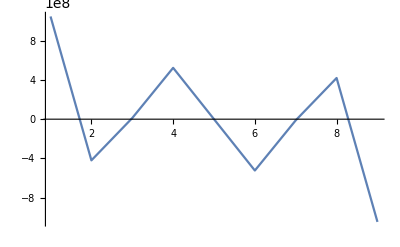

```mathematica
ListLinePlot[sdy,PlotRange->All]
```

```mathematica
ListLinePlot[sdy,PlotRange->All]
```

-Graphics-

### Band Structure

```mathematica
H1[kx_,ky_]:=H[kx,ky];
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.997, Max = 0.997

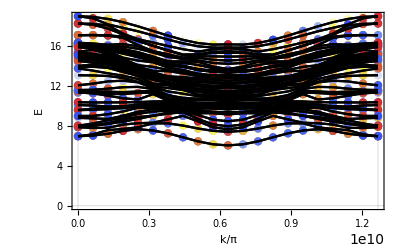

```mathematica
WBands[H1,prsz,{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.994, Max = 0.994

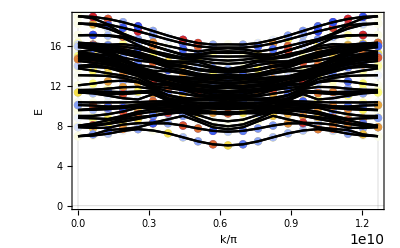

```mathematica
WBands[H1,prsx,{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.306, Max = 0.306

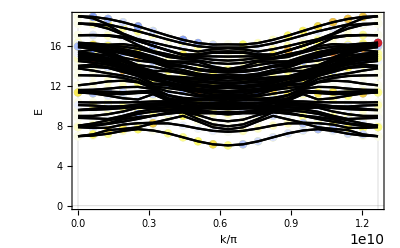

```mathematica
WBands[H1,sxL[4],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.794, Max = 0.794

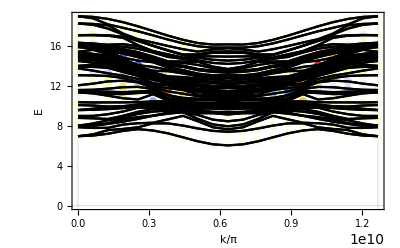

```mathematica
WBands[H1,sxL[9],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Min = -0.956, Max = 0.956

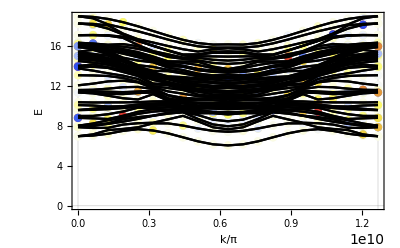

```mathematica
WBands[H1,prsy,{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

```mathematica
data=WBands[H1,prsy,"data",{{0,2 Pi/a0},{0,0},{2 Pi/a0,0}}];
```

Required variables : , , kxky.

3 Segments
, , 0.6.32911×10^91.26582×10^10

Min = -0.996, Max = 0.996

```mathematica
data[[All,All,3]]
```

{{0.00771997,-0.00699896,0.00591006,0.276295,0.0334081,-0.00486579,0.0303997,-0.0606785,-0.049938,-0.134687,0.150399,-0.0186488,0.00352811,0.011295,-0.00416691,0.0101868,0.00644407,0.00649416,0.00163439,0.00819814,0.0341478,0.995088,0.812369,0.6415,0.571345,0.465,0.498534,0.459958,0.471089,0.486481,0.609455,-0.211999,-0.868987,-0.0940409,0.327054,0.617307,-0.166283,-0.0403925,0.0790336,-0.157335,-0.0223387},{-0.00771997,0.00699896,-0.00591006,-0.276295,-0.0334081,0.00486579,-0.0303997,0.0606785,0.049938,0.134687,-0.150399,0.0186488,-0.00352811,-0.011295,0.00416691,-0.0101868,-0.00644407,-0.00649416,-0.00163439,-0.00819814,-0.0341478,-0.995088,-0.812369,-0.6415,-0.571345,-0.465,-0.498534,-0.459958,-0.471089,-0.486481,-0.609455,0.211999,0.868987,0.0940409,-0.327054,-0.617307,0.166283,0.0403925,-0.0790336,0.157335,0.0223387},{-0.000607969,0.0186401,-0.0364915,0.0621641,0.0226181,-0.072626,-0.122379,0.0380845,0.0604926,-0.0416756,0.154297,0.0015346,-0.00758496,-0.0340103,-0.0481265,-0.0454907,0.234478,0.00834444,0.00177212,0.00220491,0.0541982,0.919351,0.587126,-0.707388,0.710403,-0.705313,-0.455289,0.646706,0.527942,0.220013,0.166382,0.388665,-0.65783,-0.729713,-0.575805,0.925961,0.298081,0.515997,0.584683,0.886425,-0.000198484},{0.000607969,-0.0186401,0.0364915,-0.0621641,-0.0226181,0.072626,0.122379,-0.0380845,-0.0604926,0.0416756,-0.154297,-0.0015346,0.00758496,0.0340103,0.0481265,0.0454907,-0.234478,-0.00834444,-0.00177212,-0.00220491,-0.0541982,-0.919351,-0.587126,0.707388,-0.710403,0.705313,0.455289,-0.646706,-0.527942,-0.220013,-0.166382,-0.388665,0.65783,0.729713,0.575805,-0.925961,-0.298081,-0.515997,-0.584683,-0.886425,0.000198484},{0.576124,0.0433248,0.40761,0.161722,0.102436,-0.0689258,-0.126412,0.0129946,-0.179898,0.0361757,0.089674,-0.0051306,-0.0051056,-0.00344553,-0.0988133,0.0324774,-0.0326117,-0.000103529,0.0344785,-0.00885518,-0.0395376,0.129073,0.026312,0.076357,0.099976,0.180847,0.497612,0.330473,-0.166358,-0.674219,-0.427512,-0.585334,0.310477,-0.585996,0.479014,0.267572,-0.22064,-0.822237,-0.578779,0.134398,0.326806},{-0.576124,-0.0433248,-0.40761,-0.161722,-0.102436,0.0689258,0.126412,-0.0129946,0.179898,-0.0361757,-0.089674,0.0051306,0.0051056,0.00344553,0.0988133,-0.0324774,0.0326117,0.000103529,-0.0344785,0.00885518,0.0395376,-0.129073,-0.026312,-0.076357,-0.099976,-0.180847,-0.497612,-0.330473,0.166358,0.674219,0.427512,0.585334,-0.310477,0.585996,-0.479014,-0.267572,0.22064,0.822237,0.578779,-0.134398,-0.326806},{-0.0358742,0.0226658,-0.0533973,-0.0237697,-0.447512,0.0764117,0.193801,0.0012486,-0.147693,-0.0607189,-0.144458,0.0157374,-0.0239259,-0.406551,-0.00451375,0.173636,-0.300343,-0.00362895,0.136907,0.0494408,0.0662511,0.0175313,0.0158321,-0.097696,-0.733026,-0.841576,-0.106416,0.862855,0.863684,0.673869,0.633448,0.0547177,0.673141,-0.853355,0.0196829,0.423259,-0.534113,-0.051702,-0.266956,0.0537289,0.00598174},{0.0358742,-0.0226658,0.0533973,0.0237697,0.447512,-0.0764117,-0.193801,-0.0012486,0.147693,0.0607189,0.144458,-0.0157374,0.0239259,0.406551,0.00451375,-0.173636,0.300343,0.00362895,-0.136907,-0.0494408,-0.0662511,-0.0175313,-0.0158321,0.097696,0.733026,0.841576,0.106416,-0.862855,-0.863684,-0.673869,-0.633448,-0.0547177,-0.673141,0.853355,-0.0196829,-0.423259,0.534113,0.051702,0.266956,-0.0537289,-0.00598174},{-0.00139312,0.00912444,-0.0210795,0.0843562,0.273923,-0.17988,0.247958,0.191372,0.0575254,0.18957,0.000740188,0.218179,-0.126937,0.271964,-0.000423001,0.136262,-0.19307,0.0277537,-0.160241,-0.0121549,0.198334,-0.102257,-0.00342309,0.00761253,-0.0931787,-0.800212,-0.000602997,0.0303864,0.476615,-0.454967,-0.273716,-0.0255905,0.35638,-0.256171,0.196537,-0.511805,-0.491324,-0.781485,0.738737,0.720986,0.0301115},{0.00139312,-0.00912444,0.0210795,-0.0843562,-0.273923,0.17988,-0.247958,-0.191372,-0.0575254,-0.18957,-0.000740188,-0.218179,0.126937,-0.271964,0.000423001,-0.136262,0.19307,-0.0277537,0.160241,0.0121549,-0.198334,0.102257,0.00342309,-0.00761253,0.0931787,0.800212,0.000602997,-0.0303864,-0.476615,0.454967,0.273716,0.0255905,-0.35638,0.256171,-0.196537,0.511805,0.491324,0.781485,-0.738737,-0.720986,-0.0301115},{-0.00416676,-0.0517903,0.423355,-0.846948,-0.334013,0.0391973,-0.0251395,0.0275942,0.0904925,0.0207567,0.0188729,-0.0120864,-0.0160034,-0.0239553,0.269723,0.0025724,-0.0510695,-0.0237484,-0.173992,-0.0255151,-0.324146,-0.4666,-0.360628,0.348953,0.88043,0.0101324,-0.224768,0.871648,-0.646294,0.33658,-0.863889,0.0513698,-0.606544,-0.352979,-0.453225,0.552391,0.481013,0.124362,0.417254,0.855904,-0.0131805},{0.00416676,0.0517903,-0.423355,0.846948,0.334013,-0.0391973,0.0251395,-0.0275942,-0.0904925,-0.0207567,-0.0188729,0.0120864,0.0160034,0.0239553,-0.269723,-0.0025724,0.0510695,0.0237484,0.173992,0.0255151,0.324146,0.4666,0.360628,-0.348953,-0.88043,-0.0101324,0.224768,-0.871648,0.646294,-0.33658,0.863889,-0.0513698,0.606544,0.352979,0.453225,-0.552391,-0.481013,-0.124362,-0.417254,-0.855904,0.0131805},{-0.45855,0.0208143,-0.00950884,-0.103173,-0.0265276,-0.394454,-0.0737288,-0.722822,-0.011193,-0.178755,-0.217675,-0.106715,-0.207595,0.109113,-0.0500363,0.00965762,-0.0377436,-0.0291225,-0.0671345,-0.148013,-0.104692,0.135528,-0.923707,-0.57028,0.888272,0.0015,0.174217,0.619164,0.229884,0.326148,-0.229767,0.0760367,-0.735302,0.197379,-0.734984,-0.837845,0.256833,-0.462275,-0.290174,-0.642569,-0.670301},{0.45855,-0.0208143,0.00950884,0.103173,0.0265276,0.394454,0.0737288,0.722822,0.011193,0.178755,0.217675,0.106715,0.207595,-0.109113,0.0500363,-0.00965762,0.0377436,0.0291225,0.0671345,0.148013,0.104692,-0.135528,0.923707,0.57028,-0.888272,-0.0015,-0.174217,-0.619164,-0.229884,-0.326148,0.229767,-0.0760367,0.735302,-0.197379,0.734984,0.837845,-0.256833,0.462275,0.290174,0.642569,0.670301},{0.0212839,0.0115335,0.122662,0.106907,-0.102834,-0.0214181,0.0312382,0.0687319,-0.0167101,0.0499305,0.101185,0.0593543,0.131084,-0.0823204,0.0755813,-0.150496,-0.0991684,0.0430029,-0.0870102,0.0427807,-0.0261922,0.0165774,-0.242685,-0.0124996,-0.0158599,-0.033173,0.469816,0.675939,0.0168933,0.463674,0.432462,-0.155558,0.706869,0.187085,-0.285562,-0.600122,0.0817519,-0.298131,-0.011935,-0.0176794,-0.00615562},{-0.0212839,-0.0115335,-0.122662,-0.106907,0.102834,0.0214181,-0.0312382,-0.0687319,0.0167101,-0.0499305,-0.101185,-0.0593543,-0.131084,0.0823204,-0.0755813,0.150496,0.0991684,-0.0430029,0.0870102,-0.0427807,0.0261922,-0.0165774,0.242685,0.0124996,0.0158599,0.033173,-0.469816,-0.675939,-0.0168933,-0.463674,-0.432462,0.155558,-0.706869,-0.187085,0.285562,0.600122,-0.0817519,0.298131,0.011935,0.0176794,0.00615562},{-0.0121244,0.128523,0.0388889,-0.0234052,0.191938,-0.0437667,-0.0373385,0.422487,0.00765343,-0.446905,0.0978198,0.0354573,0.485641,0.0142093,0.0990802,-0.034526,-0.0517204,0.0293698,-0.148877,0.0000157219,0.00541299,0.305268,0.4683,-0.432458,-0.148951,-0.00709842,-0.748293,0.390143,0.252752,0.889057,-0.012691,-0.321774,-0.513668,0.863938,0.422685,0.869615,0.232998,0.228865,0.622198,-0.763217,-0.00916259},{0.0121244,-0.128523,-0.0388889,0.0234052,-0.191938,0.0437667,0.0373385,-0.422487,-0.00765343,0.446905,-0.0978198,-0.0354573,-0.485641,-0.0142093,-0.0990802,0.034526,0.0517204,-0.0293698,0.148877,-0.0000157219,-0.00541299,-0.305268,-0.4683,0.432458,0.148951,0.00709842,0.748293,-0.390143,-0.252752,-0.889057,0.012691,0.321774,0.513668,-0.863938,-0.422685,-0.869615,-0.232998,-0.228865,-0.622198,0.763217,0.00916259},{-0.000821169,-0.102132,0.129193,0.11192,-0.0823132,-0.15908,-0.00938519,-0.330744,0.126503,-0.0544853,-0.0643704,0.00997356,0.0775084,-0.0235888,0.0447567,-0.015064,0.0386443,-0.0130413,0.155069,-0.155814,0.0261073,0.249212,0.252215,-0.400723,-0.767434,-0.375356,0.306011,0.142098,-0.355354,-0.275848,0.0103284,-0.678011,-0.15675,0.468838,0.275751,-0.12155,0.268177,-0.401792,0.145319,0.217167,-0.00131107},{0.000821169,0.102132,-0.129193,-0.11192,0.0823132,0.15908,0.00938519,0.330744,-0.126503,0.0544853,0.0643704,-0.00997356,-0.0775084,0.0235888,-0.0447567,0.015064,-0.0386443,0.0130413,-0.155069,0.155814,-0.0261073,-0.249212,-0.252215,0.400723,0.767434,0.375356,-0.306011,-0.142098,0.355354,0.275848,-0.0103284,0.678011,0.15675,-0.468838,-0.275751,0.12155,-0.268177,0.401792,-0.145319,-0.217167,0.00131107},{0.329743,0.00220126,-0.139918,0.41316,-0.3415,0.0253859,-0.427599,-0.112699,-0.404035,0.26432,-0.118751,-0.00179526,0.0486447,-0.11006,-0.068408,0.437663,-0.0167758,-0.184993,0.0365183,0.000581331,0.00386338,-0.114479,0.0261191,0.113213,-0.0755489,0.0000622641,-0.376585,0.296075,0.0673187,0.552045,0.842766,0.942534,0.701435,-0.649963,0.825752,-0.975345,0.318207,-0.671433,-0.908973,0.592856,-0.60673},{-0.329743,-0.00220126,0.139918,-0.41316,0.3415,-0.0253859,0.427599,0.112699,0.404035,-0.26432,0.118751,0.00179526,-0.0486447,0.11006,0.068408,-0.437663,0.0167758,0.184993,-0.0365183,-0.000581331,-0.00386338,0.114479,-0.0261191,-0.113213,0.0755489,-0.0000622641,0.376585,-0.296075,-0.0673187,-0.552045,-0.842766,-0.942534,-0.701435,0.649963,-0.825752,0.975345,-0.318207,0.671433,0.908973,-0.592856,0.60673},{-0.0523651,-0.0130593,0.0814096,-0.0650554,-0.0356928,0.0045936,-0.0368078,0.094287,-0.139654,-0.0840635,0.00184109,0.00159556,-0.037289,0.0506208,-0.0132741,0.0768632,-0.0568351,-0.165836,-0.456704,-0.14053,-0.295169,0.113887,0.0515722,0.331369,0.18213,0.24267,0.138204,0.391949,-0.776397,-0.890499,0.716563,-0.904474,0.213143,-0.24726,-0.276282,-0.694266,0.0291847,-0.543483,0.0546312,0.0313002,0.00035811},{0.0523651,0.0130593,-0.0814096,0.0650554,0.0356928,-0.0045936,0.0368078,-0.094287,0.139654,0.0840635,-0.00184109,-0.00159556,0.037289,-0.0506208,0.0132741,-0.0768632,0.0568351,0.165836,0.456704,0.14053,0.295169,-0.113887,-0.0515722,-0.331369,-0.18213,-0.24267,-0.138204,-0.391949,0.776397,0.890499,-0.716563,0.904474,-0.213143,0.24726,0.276282,0.694266,-0.0291847,0.543483,-0.0546312,-0.0313002,-0.00035811},{-0.680546,0.0851163,-0.113765,-0.61848,0.0558409,0.0430216,-0.141847,-0.11291,-0.0996098,0.0399725,-0.169717,-0.216152,0.0130917,-0.507514,0.00176823,-0.115678,-0.0241697,0.00731231,0.146141,-0.0296868,0.0271846,-0.158434,0.175786,-0.183251,0.394016,-0.387146,0.06198,-0.0779188,-0.590348,-0.153824,-0.744957,0.555357,-0.378205,0.265796,-0.677004,-0.574888,-0.580236,-0.661854,-0.141961,0.232737,-0.45717},{0.680546,-0.0851163,0.113765,0.61848,-0.0558409,-0.0430216,0.141847,0.11291,0.0996098,-0.0399725,0.169717,0.216152,-0.0130917,0.507514,-0.00176823,0.115678,0.0241697,-0.00731231,-0.146141,0.0296868,-0.0271846,0.158434,-0.175786,0.183251,-0.394016,0.387146,-0.06198,0.0779188,0.590348,0.153824,0.744957,-0.555357,0.378205,-0.265796,0.677004,0.574888,0.580236,0.661854,0.141961,-0.232737,0.45717},{0.0619127,-0.712679,-0.747998,0.568724,0.12903,-0.159343,-0.0200213,-0.537229,-0.0415344,0.0982448,0.0773574,0.0572001,0.0709045,0.144071,0.330838,0.0566601,-0.0074493,0.00305435,0.00423464,0.00192083,-0.357101,-0.604725,-0.704448,-0.678272,0.449785,0.487114,-0.181704,0.258747,0.371464,-0.15192,-0.587308,0.483337,-0.639399,0.43358,0.415837,-0.0374993,-0.100925,-0.088936,0.0664868,0.411158,0.00453686},{-0.0619127,0.712679,0.747998,-0.568724,-0.12903,0.159343,0.0200213,0.537229,0.0415344,-0.0982448,-0.0773574,-0.0572001,-0.0709045,-0.144071,-0.330838,-0.0566601,0.0074493,-0.00305435,-0.00423464,-0.00192083,0.357101,0.604725,0.704448,0.678272,-0.449785,-0.487114,0.181704,-0.258747,-0.371464,0.15192,0.587308,-0.483337,0.639399,-0.43358,-0.415837,0.0374993,0.100925,0.088936,-0.0664868,-0.411158,-0.00453686},{-0.00829179,0.0765275,0.0824768,-0.0838379,0.351779,-0.301805,-0.124791,-0.271042,-0.069654,-0.0156457,0.00421979,0.182353,0.00616026,0.00879127,0.0601968,-0.0324672,-0.0909352,-0.0226746,0.00113392,0.0131325,-0.0835858,0.784018,-0.449151,-0.416686,-0.112489,0.127545,0.00560994,-0.596994,0.753911,0.516134,-0.504026,-0.774015,0.482961,0.26664,0.826879,0.830791,0.489084,-0.838959,-0.23889,-0.690523,0.00305921},{0.00829179,-0.0765275,-0.0824768,0.0838379,-0.351779,0.301805,0.124791,0.271042,0.069654,0.0156457,-0.00421979,-0.182353,-0.00616026,-0.00879127,-0.0601968,0.0324672,0.0909352,0.0226746,-0.00113392,-0.0131325,0.0835858,-0.784018,0.449151,0.416686,0.112489,-0.127545,-0.00560994,0.596994,-0.753911,-0.516134,0.504026,0.774015,-0.482961,-0.26664,-0.826879,-0.830791,-0.489084,0.838959,0.23889,0.690523,-0.00305921},{-0.100599,-0.0322551,0.0456438,-0.205627,-0.197393,-0.00982353,-0.033248,0.124789,-0.00442247,0.205126,0.0786592,-0.0545759,0.101451,-0.11217,-0.0101693,0.136052,-0.117614,0.0407487,-0.124995,0.00149735,-0.117366,-0.188926,0.00990016,-0.0708371,0.271013,-0.554717,0.169928,0.555853,0.871295,-0.493102,0.0141545,-0.186663,-0.876129,0.759954,0.837598,0.379834,-0.564132,0.0678889,-0.215195,-0.0145908,0.00819819},{0.100599,0.0322551,-0.0456438,0.205627,0.197393,0.00982353,0.033248,-0.124789,0.00442247,-0.205126,-0.0786592,0.0545759,-0.101451,0.11217,0.0101693,-0.136052,0.117614,-0.0407487,0.124995,-0.00149735,0.117366,0.188926,-0.00990016,0.0708371,-0.271013,0.554717,-0.169928,-0.555853,-0.871295,0.493102,-0.0141545,0.186663,0.876129,-0.759954,-0.837598,-0.379834,0.564132,-0.0678889,0.215195,0.0145908,-0.00819819},{0.100128,0.00180187,0.00906503,0.0799206,-0.0286883,0.202291,0.0106815,0.0518155,-0.545164,0.191615,0.116676,0.0341078,0.135049,0.19526,0.364483,0.160006,0.00948193,0.118909,0.0205062,-0.060317,-0.0269458,0.00062666,-0.0325361,-0.290803,0.0775702,0.363894,0.459484,-0.168576,-0.560924,0.82435,0.0829084,0.478498,0.414529,-0.722934,-0.700938,0.939954,0.704568,-0.458563,-0.200884,-0.135265,0.031311},{-0.100128,-0.00180187,-0.00906503,-0.0799206,0.0286883,-0.202291,-0.0106815,-0.0518155,0.545164,-0.191615,-0.116676,-0.0341078,-0.135049,-0.19526,-0.364483,-0.160006,-0.00948193,-0.118909,-0.0205062,0.060317,0.0269458,-0.00062666,0.0325361,0.290803,-0.0775702,-0.363894,-0.459484,0.168576,0.560924,-0.82435,-0.0829084,-0.478498,-0.414529,0.722934,0.700938,-0.939954,-0.704568,0.458563,0.200884,0.135265,-0.031311},{-0.0917193,0.0137604,-0.0274642,0.0162732,0.00198925,-0.564735,-0.0366697,-0.34092,0.0202675,-0.00128416,-0.179288,-0.04975,0.023008,-0.0432529,-0.106715,-0.0294635,-0.136581,0.109308,-0.0229446,-0.0887957,0.0803428,0.285725,0.463189,0.694226,-0.777258,0.14718,-0.175138,-0.026255,0.689175,-0.354885,0.580873,0.429238,-0.592552,0.0564969,0.489243,-0.104038,0.0110292,0.126851,0.10989,0.0328574,0.0572709},{0.0917193,-0.0137604,0.0274642,-0.0162732,-0.00198925,0.564735,0.0366697,0.34092,-0.0202675,0.00128416,0.179288,0.04975,-0.023008,0.0432529,0.106715,0.0294635,0.136581,-0.109308,0.0229446,0.0887957,-0.0803428,-0.285725,-0.463189,-0.694226,0.777258,-0.14718,0.175138,0.026255,-0.689175,0.354885,-0.580873,-0.429238,0.592552,-0.0564969,-0.489243,0.104038,-0.0110292,-0.126851,-0.10989,-0.0328574,-0.0572709},{-0.00189592,-0.0663303,0.201385,0.197275,0.227421,-0.0787817,0.0542837,0.0172797,-0.226577,0.177274,0.229961,-0.0711555,0.00684972,-0.0548731,-0.110741,-0.532436,-0.0116711,-0.00999666,0.000809386,-0.091282,-0.826863,0.601598,-0.436698,0.471425,-0.792358,-0.510352,-0.259394,-0.792667,-0.859363,-0.671459,0.514255,-0.0121114,0.00915381,-0.191685,0.776074,0.565661,0.46166,0.201309,-0.235634,0.259484,-0.000946224},{0.00189592,0.0663303,-0.201385,-0.197275,-0.227421,0.0787817,-0.0542837,-0.0172797,0.226577,-0.177274,-0.229961,0.0711555,-0.00684972,0.0548731,0.110741,0.532436,0.0116711,0.00999666,-0.000809386,0.091282,0.826863,-0.601598,0.436698,-0.471425,0.792358,0.510352,0.259394,0.792667,0.859363,0.671459,-0.514255,0.0121114,-0.00915381,0.191685,-0.776074,-0.565661,-0.46166,-0.201309,0.235634,-0.259484,0.000946224},{-0.29419,-0.0186623,0.0500646,-0.0133974,0.0519233,-0.00522291,-0.126226,-0.0155458,-0.0970608,0.234066,0.116555,-0.00695863,-0.0452947,-0.0928074,-0.0928112,-0.0572869,-0.145258,0.0458056,-0.429603,0.13118,0.119096,-0.826065,-0.0740019,0.704697,-0.826843,-0.70166,0.87367,-0.0712844,0.279501,-0.379643,0.0764369,0.404581,-0.00572771,0.11963,0.28144,0.4019,-0.179295,-0.0860523,-0.349862,-0.437578,-0.206321},{0.29419,0.0186623,-0.0500646,0.0133974,-0.0519233,0.00522291,0.126226,0.0155458,0.0970608,-0.234066,-0.116555,0.00695863,0.0452947,0.0928074,0.0928112,0.0572869,0.145258,-0.0458056,0.429603,-0.13118,-0.119096,0.826065,0.0740019,-0.704697,0.826843,0.70166,-0.87367,0.0712844,-0.279501,0.379643,-0.0764369,-0.404581,0.00572771,-0.11963,-0.28144,-0.4019,0.179295,0.0860523,0.349862,0.437578,0.206321},{-0.179714,-0.00183575,-0.047062,-0.201966,-0.0775087,0.0156041,-0.0445527,-0.0222964,0.0441973,-0.170937,0.000163399,-0.0125184,-0.00750731,0.225411,-0.0818733,0.121623,0.383978,0.0168472,-0.0303211,-0.017952,0.0131159,-0.0000950627,0.231565,-0.429573,0.345222,0.533075,0.622933,0.869185,0.767443,0.78052,0.940046,0.489422,0.075378,-0.00909438,0.561447,0.389998,-0.80328,0.634951,0.87492,-0.384116,0.2803},{0.179714,0.00183575,0.047062,0.201966,0.0775087,-0.0156041,0.0445527,0.0222964,-0.0441973,0.170937,-0.000163399,0.0125184,0.00750731,-0.225411,0.0818733,-0.121623,-0.383978,-0.0168472,0.0303211,0.017952,-0.0131159,0.0000950627,-0.231565,0.429573,-0.345222,-0.533075,-0.622933,-0.869185,-0.767443,-0.78052,-0.940046,-0.489422,-0.075378,0.00909438,-0.561447,-0.389998,0.80328,-0.634951,-0.87492,0.384116,-0.2803},{0.0140221,0.00231898,0.115965,0.010293,0.00176966,0.0791527,-0.287029,-0.306299,-0.205511,0.00233224,-0.0778174,-0.0882653,-0.0122848,-0.00857675,-0.0803364,0.0193146,-0.032321,0.132208,0.0273696,0.221647,-0.0196134,-0.389175,-0.525487,-0.454335,-0.000848542,0.752794,0.392886,0.620545,-0.663779,0.0261815,0.186403,-0.00779952,-0.0442775,0.13126,0.326796,0.753623,0.163767,0.600167,-0.34712,-0.212709,-0.0133845},{-0.0140221,-0.00231898,-0.115965,-0.010293,-0.00176966,-0.0791527,0.287029,0.306299,0.205511,-0.00233224,0.0778174,0.0882653,0.0122848,0.00857675,0.0803364,-0.0193146,0.032321,-0.132208,-0.0273696,-0.221647,0.0196134,0.389175,0.525487,0.454335,0.000848542,-0.752794,-0.392886,-0.620545,0.663779,-0.0261815,-0.186403,0.00779952,0.0442775,-0.13126,-0.326796,-0.753623,-0.163767,-0.600167,0.34712,0.212709,0.0133845},{-0.070476,0.0625547,-0.0176691,0.0943534,-0.0573761,-0.00995105,-0.112823,-0.00839111,-0.0158594,0.0865504,0.229584,-0.337467,-0.0317695,-0.0000268708,-0.0848414,0.132709,0.0563136,-0.0311855,0.0678098,-0.0478611,0.0529844,0.245197,-0.599265,0.298792,-0.0574379,-0.291389,0.0538453,0.0727767,0.283791,0.612778,-0.205292,-0.107071,-0.281664,0.104869,-0.252579,-0.613243,-0.211018,0.0580966,-0.742847,0.885073,-0.378756},{0.070476,-0.0625547,0.0176691,-0.0943534,0.0573761,0.00995105,0.112823,0.00839111,0.0158594,-0.0865504,-0.229584,0.337467,0.0317695,0.0000268708,0.0848414,-0.132709,-0.0563136,0.0311855,-0.0678098,0.0478611,-0.0529844,-0.245197,0.599265,-0.298792,0.0574379,0.291389,-0.0538453,-0.0727767,-0.283791,-0.612778,0.205292,0.107071,0.281664,-0.104869,0.252579,0.613243,0.211018,-0.0580966,0.742847,-0.885073,0.378756},{-0.0517178,-0.0455862,0.107983,-0.0115711,-0.0303777,0.0162413,-0.0507956,-0.0295532,0.363137,0.790276,0.169745,0.0759208,-0.156009,0.211247,0.00453527,-0.223497,-0.025642,0.509575,0.261066,-0.000390516,0.0153943,-0.179789,0.184853,-0.152504,-0.00308282,0.227372,0.27972,-0.0546219,-0.0506099,-0.417614,-0.430801,0.386316,0.44421,-0.0237216,0.0243738,0.861448,0.710462,-0.256664,0.41017,0.0355185,-0.0284959},{0.0517178,0.0455862,-0.107983,0.0115711,0.0303777,-0.0162413,0.0507956,0.0295532,-0.363137,-0.790276,-0.169745,-0.0759208,0.156009,-0.211247,-0.00453527,0.223497,0.025642,-0.509575,-0.261066,0.000390516,-0.0153943,0.179789,-0.184853,0.152504,0.00308282,-0.227372,-0.27972,0.0546219,0.0506099,0.417614,0.430801,-0.386316,-0.44421,0.0237216,-0.0243738,-0.861448,-0.710462,0.256664,-0.41017,-0.0355185,0.0284959},{-0.221038,0.728336,0.0756283,0.0649246,-0.298059,-0.255151,-0.0326924,0.143147,-0.0151056,0.288203,0.0044633,-0.158375,0.0226017,-0.000939273,-0.0222208,-0.0106296,-0.0200116,0.00625028,0.0562221,0.0303125,-0.0790763,0.00454293,-0.0775591,0.476347,0.453714,-0.0405365,0.120122,0.08747,-0.0778765,0.163936,-0.0310932,0.641517,0.447092,-0.1297,0.232347,-0.528254,-0.469723,-0.145305,-0.324952,-0.0229708,-0.350901},{0.221038,-0.728336,-0.0756283,-0.0649246,0.298059,0.255151,0.0326924,-0.143147,0.0151056,-0.288203,-0.0044633,0.158375,-0.0226017,0.000939273,0.0222208,0.0106296,0.0200116,-0.00625028,-0.0562221,-0.0303125,0.0790763,-0.00454293,0.0775591,-0.476347,-0.453714,0.0405365,-0.120122,-0.08747,0.0778765,-0.163936,0.0310932,-0.641517,-0.447092,0.1297,-0.232347,0.528254,0.469723,0.145305,0.324952,0.0229708,0.350901},{0.294669,0.137797,-0.357151,-0.153323,-0.0139541,0.022438,0.124586,-0.0705157,0.0109895,0.0121471,0.0528599,-0.0337998,0.42487,0.0245142,0.00719829,-0.0263168,-0.0131518,0.111979,-0.0745251,-0.0177502,-0.0192827,-0.110894,-0.257364,-0.370059,-0.0781533,0.226198,0.267246,-0.781928,0.0793213,-0.0155008,-0.497076,-0.194946,-0.233248,-0.633307,-0.119812,0.316673,0.00537021,0.313084,-0.0756187,-0.146872,0.0421791},{-0.294669,-0.137797,0.357151,0.153323,0.0139541,-0.022438,-0.124586,0.0705157,-0.0109895,-0.0121471,-0.0528599,0.0337998,-0.42487,-0.0245142,-0.00719829,0.0263168,0.0131518,-0.111979,0.0745251,0.0177502,0.0192827,0.110894,0.257364,0.370059,0.0781533,-0.226198,-0.267246,0.781928,-0.0793213,0.0155008,0.497076,0.194946,0.233248,0.633307,0.119812,-0.316673,-0.00537021,-0.313084,0.0756187,0.146872,-0.0421791},{0.456932,-0.0359239,0.358776,0.333662,-0.0195622,0.0342388,0.00880986,0.0439245,0.035152,0.0385464,-0.037047,0.0225816,-0.0118637,0.142033,-0.108273,-0.114,0.0854562,0.1608,0.0626292,0.102628,-0.837704,0.0998276,-0.496876,0.791027,0.136204,-0.745735,-0.309685,-0.496157,0.816709,0.685152,-0.776147,0.43017,0.514411,-0.28372,0.215726,0.0236057,-0.248129,-0.564771,-0.456339,0.0271418,-0.440606},{-0.456932,0.0359239,-0.358776,-0.333662,0.0195622,-0.0342388,-0.00880986,-0.0439245,-0.035152,-0.0385464,0.037047,-0.0225816,0.0118637,-0.142033,0.108273,0.114,-0.0854562,-0.1608,-0.0626292,-0.102628,0.837704,-0.0998276,0.496876,-0.791027,-0.136204,0.745735,0.309685,0.496157,-0.816709,-0.685152,0.776147,-0.43017,-0.514411,0.28372,-0.215726,-0.0236057,0.248129,0.564771,0.456339,-0.0271418,0.440606},{-0.233291,-0.0737587,-0.0394114,0.0136265,0.190657,0.0226067,-0.630295,-0.0111322,0.222631,0.0974638,-0.0259195,-0.0234003,-0.0325287,0.470142,-0.27503,-0.402832,0.0560675,-0.0660618,0.0253046,0.0540456,0.0995196,0.385224,-0.169186,0.000397207,0.470527,0.0585628,-0.269495,0.761496,-0.187532,-0.76073,-0.543701,-0.46962,0.24528,-0.223243,0.272172,0.24536,0.0501932,0.0524843,-0.324144,0.090975,-0.00575587},{0.233291,0.0737587,0.0394114,-0.0136265,-0.190657,-0.0226067,0.630295,0.0111322,-0.222631,-0.0974638,0.0259195,0.0234003,0.0325287,-0.470142,0.27503,0.402832,-0.0560675,0.0660618,-0.0253046,-0.0540456,-0.0995196,-0.385224,0.169186,-0.000397207,-0.470527,-0.0585628,0.269495,-0.761496,0.187532,0.76073,0.543701,0.46962,-0.24528,0.223243,-0.272172,-0.24536,-0.0501932,-0.0524843,0.324144,-0.090975,0.00575587},{0.112738,-0.379497,-0.0767732,0.250643,-0.0445358,-0.300989,0.0000372946,-0.015285,-0.339373,0.0662878,0.161565,-0.0656827,0.0368057,0.0588347,-0.249906,0.0624914,0.0608768,-0.0268827,-0.113017,0.0199511,-0.0022113,0.0623995,-0.294619,0.0006348,-0.0670435,-0.166973,-0.263499,0.292689,0.211673,0.487029,-0.386016,-0.324495,-0.243164,-0.0198294,-0.0225852,-0.620432,-0.410486,0.203602,0.821675,0.665504,0.000927177},{-0.112738,0.379497,0.0767732,-0.250643,0.0445358,0.300989,-0.0000372946,0.015285,0.339373,-0.0662878,-0.161565,0.0656827,-0.0368057,-0.0588347,0.249906,-0.0624914,-0.0608768,0.0268827,0.113017,-0.0199511,0.0022113,-0.0623995,0.294619,-0.0006348,0.0670435,0.166973,0.263499,-0.292689,-0.211673,-0.487029,0.386016,0.324495,0.243164,0.0198294,0.0225852,0.620432,0.410486,-0.203602,-0.821675,-0.665504,-0.000927177},{-0.0074294,0.122828,0.437836,0.0885777,0.260192,-0.195723,-0.00239416,0.000445044,-0.0188737,-0.00567952,-0.0353717,0.041993,0.137893,-0.23705,-0.388739,0.0260708,-0.0118837,0.0633654,0.0574945,-0.044343,-0.0639639,0.194689,0.741741,0.0835598,0.0284016,-0.314491,-0.0653584,-0.679141,-0.166001,0.15344,-0.29368,-0.63063,0.126874,-0.4626,-0.364216,-0.481651,-0.38458,0.865792,-0.107271,0.173902,-0.00463908},{0.0074294,-0.122828,-0.437836,-0.0885777,-0.260192,0.195723,0.00239416,-0.000445044,0.0188737,0.00567952,0.0353717,-0.041993,-0.137893,0.23705,0.388739,-0.0260708,0.0118837,-0.0633654,-0.0574945,0.044343,0.0639639,-0.194689,-0.741741,-0.0835598,-0.0284016,0.314491,0.0653584,0.679141,0.166001,-0.15344,0.29368,0.63063,-0.126874,0.4626,0.364216,0.481651,0.38458,-0.865792,0.107271,-0.173902,0.00463908},{0.0510698,-0.0471434,-0.0720401,-0.199497,0.188127,-0.0202922,0.0004661,-0.169155,0.000877361,-0.0755027,0.0213353,-0.0470714,0.138192,0.616547,0.0272007,-0.289738,0.0457667,0.000990548,0.285771,-0.260758,0.945559,0.148737,-0.617919,-0.0406005,0.520391,0.123312,-0.0280037,0.0520205,-0.502444,0.0172752,0.19402,-0.784986,-0.828315,-0.104145,-0.535677,0.546609,0.136586,-0.133522,-0.489257,-0.468905,0.0472693},{-0.0510698,0.0471434,0.0720401,0.199497,-0.188127,0.0202922,-0.0004661,0.169155,-0.000877361,0.0755027,-0.0213353,0.0470714,-0.138192,-0.616547,-0.0272007,0.289738,-0.0457667,-0.000990548,-0.285771,0.260758,-0.945559,-0.148737,0.617919,0.0406005,-0.520391,-0.123312,0.0280037,-0.0520205,0.502444,-0.0172752,-0.19402,0.784986,0.828315,0.104145,0.535677,-0.546609,-0.136586,0.133522,0.489257,0.468905,-0.0472693},{0.732747,0.146428,0.145214,-0.000648228,0.0461836,-0.139053,0.00099457,0.157752,-0.175747,0.0299366,0.0586882,-0.13388,-0.00712599,0.426953,-0.631851,-0.173791,0.403138,0.118941,-0.0737814,0.097221,0.0964747,0.662095,-0.948229,-0.0906316,0.121027,-0.471824,0.0406863,-0.221022,0.287121,-0.613859,-0.883532,-0.0409329,-0.777152,0.0150094,0.855369,-0.0621839,0.00428948,0.583624,0.524346,0.547426,-0.0258624},{-0.732747,-0.146428,-0.145214,0.000648228,-0.0461836,0.139053,-0.00099457,-0.157752,0.175747,-0.0299366,-0.0586882,0.13388,0.00712599,-0.426953,0.631851,0.173791,-0.403138,-0.118941,0.0737814,-0.097221,-0.0964747,-0.662095,0.948229,0.0906316,-0.121027,0.471824,-0.0406863,0.221022,-0.287121,0.613859,0.883532,0.0409329,0.777152,-0.0150094,-0.855369,0.0621839,-0.00428948,-0.583624,-0.524346,-0.547426,0.0258624},{-0.128499,-0.244854,-0.000492856,-0.0730579,0.372749,-0.0391539,-0.0147491,0.191102,0.318103,-0.177098,-0.00393014,0.149269,-0.146139,-0.0975339,-0.0760895,0.00171798,0.204386,-0.13138,-0.0820709,0.0170025,-0.360872,0.251076,0.304476,0.0472626,0.393179,0.0183096,0.218453,0.0759959,0.460315,-0.459457,-0.0908539,-0.436491,-0.895521,0.368451,0.0822576,0.283017,0.193768,-0.313565,-0.316836,0.586853,0.203052},{0.128499,0.244854,0.000492856,0.0730579,-0.372749,0.0391539,0.0147491,-0.191102,-0.318103,0.177098,0.00393014,-0.149269,0.146139,0.0975339,0.0760895,-0.00171798,-0.204386,0.13138,0.0820709,-0.0170025,0.360872,-0.251076,-0.304476,-0.0472626,-0.393179,-0.0183096,-0.218453,-0.0759959,-0.460315,0.459457,0.0908539,0.436491,0.895521,-0.368451,-0.0822576,-0.283017,-0.193768,0.313565,0.316836,-0.586853,-0.203052},{0.29755,0.210254,0.0707753,0.114419,0.0183895,0.0769817,-0.0167689,0.0179067,-0.0175136,-0.237854,-0.249838,0.0210571,-0.118509,0.127474,-0.508624,-0.0039961,-0.0510459,-0.100867,0.109344,0.479123,-0.0249625,-0.199145,0.225677,0.353924,-0.37813,0.0776265,-0.380126,-0.255879,0.0189683,-0.687696,-0.163485,-0.917023,-0.767126,-0.629396,0.271784,-0.540645,0.477948,0.690226,-0.718066,-0.575783,-0.582438},{-0.29755,-0.210254,-0.0707753,-0.114419,-0.0183895,-0.0769817,0.0167689,-0.0179067,0.0175136,0.237854,0.249838,-0.0210571,0.118509,-0.127474,0.508624,0.0039961,0.0510459,0.100867,-0.109344,-0.479123,0.0249625,0.199145,-0.225677,-0.353924,0.37813,-0.0776265,0.380126,0.255879,-0.0189683,0.687696,0.163485,0.917023,0.767126,0.629396,-0.271784,0.540645,-0.477948,-0.690226,0.718066,0.575783,0.582438},{-0.0260902,-0.143679,-0.174308,0.0534457,0.493024,0.110526,-0.123443,0.00525781,0.00226168,0.0698729,-0.049924,-0.0870179,-0.0831657,-0.043959,0.811729,-0.568988,-0.177409,-0.00373351,-0.000876528,-0.0267116,0.000907893,0.122834,0.0303175,0.0371714,-0.880427,-0.111036,-0.421343,-0.165152,-0.1525,-0.108147,0.0184389,0.412448,-0.683763,-0.0785578,0.142357,-0.550105,0.882905,0.0185371,0.469307,-0.683462,0.196277},{0.0260902,0.143679,0.174308,-0.0534457,-0.493024,-0.110526,0.123443,-0.00525781,-0.00226168,-0.0698729,0.049924,0.0870179,0.0831657,0.043959,-0.811729,0.568988,0.177409,0.00373351,0.000876528,0.0267116,-0.000907893,-0.122834,-0.0303175,-0.0371714,0.880427,0.111036,0.421343,0.165152,0.1525,0.108147,-0.0184389,-0.412448,0.683763,0.0785578,-0.142357,0.550105,-0.882905,-0.0185371,-0.469307,0.683462,-0.196277},{0.0905685,0.160023,0.129289,0.0182074,0.057405,0.0273829,0.00379852,-0.0023922,-0.20878,0.0135366,0.263855,0.233056,0.131698,-0.312731,-0.404131,0.0881819,-0.0111135,-0.59005,-0.00287881,-0.138725,0.0221768,0.519269,0.669593,-0.26895,-0.734387,0.884475,-0.622936,0.448456,0.51843,0.0783296,-0.10598,-0.0193193,-0.320239,-0.0411605,-0.567481,0.42656,-0.126265,0.174284,-0.589164,-0.329637,-0.271491},{-0.0905685,-0.160023,-0.129289,-0.0182074,-0.057405,-0.0273829,-0.00379852,0.0023922,0.20878,-0.0135366,-0.263855,-0.233056,-0.131698,0.312731,0.404131,-0.0881819,0.0111135,0.59005,0.00287881,0.138725,-0.0221768,-0.519269,-0.669593,0.26895,0.734387,-0.884475,0.622936,-0.448456,-0.51843,-0.0783296,0.10598,0.0193193,0.320239,0.0411605,0.567481,-0.42656,0.126265,-0.174284,0.589164,0.329637,0.271491},{0.0289478,-0.0744624,0.0095502,-0.00323538,0.0437652,-0.0414842,-0.0406502,0.11597,-0.497792,-0.0254238,-0.14637,0.014938,0.308683,0.0942006,-0.362174,-0.182644,0.088058,0.523018,0.64619,-0.104658,0.571744,-0.605092,-0.0990548,-0.264309,0.159012,0.179608,-0.229167,-0.183545,0.46964,0.073048,-0.231046,0.0456066,-0.11084,0.575647,-0.628382,-0.40044,0.207585,0.224102,-0.426002,-0.0234681,0.0432451},{-0.0289478,0.0744624,-0.0095502,0.00323538,-0.0437652,0.0414842,0.0406502,-0.11597,0.497792,0.0254238,0.14637,-0.014938,-0.308683,-0.0942006,0.362174,0.182644,-0.088058,-0.523018,-0.64619,0.104658,-0.571744,0.605092,0.0990548,0.264309,-0.159012,-0.179608,0.229167,0.183545,-0.46964,-0.073048,0.231046,-0.0456066,0.11084,-0.575647,0.628382,0.40044,-0.207585,-0.224102,0.426002,0.0234681,-0.0432451},{0.163876,0.00224652,0.00772518,0.0236177,-0.0977502,0.0835187,0.0278814,0.407129,-0.0102458,0.156361,-0.561889,0.253513,-0.0328091,0.794083,0.0719771,-0.218117,0.0703211,-0.0400743,0.0894466,-0.0487491,-0.0142042,0.000565132,-0.0263226,0.132644,-0.00600601,0.503434,-0.0808671,-0.388594,-0.242866,-0.329299,0.0383978,-0.226589,0.491321,-0.922428,-0.757506,-0.133583,0.784626,0.179487,-0.820552,-0.0697826,-0.0195612},{-0.163876,-0.00224652,-0.00772518,-0.0236177,0.0977502,-0.0835187,-0.0278814,-0.407129,0.0102458,-0.156361,0.561889,-0.253513,0.0328091,-0.794083,-0.0719771,0.218117,-0.0703211,0.0400743,-0.0894466,0.0487491,0.0142042,-0.000565132,0.0263226,-0.132644,0.00600601,-0.503434,0.0808671,0.388594,0.242866,0.329299,-0.0383978,0.226589,-0.491321,0.922428,0.757506,0.133583,-0.784626,-0.179487,0.820552,0.0697826,0.0195612},{-0.0148519,0.0213329,-0.14113,0.0241688,-0.0912703,-0.055571,0.505781,0.0248692,0.732822,-0.0543262,0.0123278,0.0503079,-0.471112,0.163558,-0.0519993,-0.704904,0.141011,0.112311,-0.0146429,-0.00844986,-0.000284947,0.000634986,-0.137512,0.384113,-0.447238,-0.649178,-0.269572,-0.363991,-0.263616,-0.602763,-0.348311,0.16941,-0.0517438,0.143217,-0.623324,0.0686787,-0.328497,-0.316726,0.0541129,0.127572,-0.155181},{0.0148519,-0.0213329,0.14113,-0.0241688,0.0912703,0.055571,-0.505781,-0.0248692,-0.732822,0.0543262,-0.0123278,-0.0503079,0.471112,-0.163558,0.0519993,0.704904,-0.141011,-0.112311,0.0146429,0.00844986,0.000284947,-0.000634986,0.137512,-0.384113,0.447238,0.649178,0.269572,0.363991,0.263616,0.602763,0.348311,-0.16941,0.0517438,-0.143217,0.623324,-0.0686787,0.328497,0.316726,-0.0541129,-0.127572,0.155181},{-0.00616305,-0.0661199,-0.16257,0.302918,-0.213633,0.221389,0.0111406,-0.319588,-0.307686,-0.00243671,-0.379055,0.146457,-0.0970058,-0.0636669,0.164994,-0.0917249,-0.00101763,0.060325,0.084892,-0.0134787,0.00111393,0.0146617,0.137993,0.102619,-0.334562,0.343997,0.266147,0.202749,-0.349978,-0.372925,0.186132,-0.264902,0.211951,0.00185392,0.139669,0.139703,0.167675,0.215943,0.682773,0.683389,0.00508075},{0.00616305,0.0661199,0.16257,-0.302918,0.213633,-0.221389,-0.0111406,0.319588,0.307686,0.00243671,0.379055,-0.146457,0.0970058,0.0636669,-0.164994,0.0917249,0.00101763,-0.060325,-0.084892,0.0134787,-0.00111393,-0.0146617,-0.137993,-0.102619,0.334562,-0.343997,-0.266147,-0.202749,0.349978,0.372925,-0.186132,0.264902,-0.211951,-0.00185392,-0.139669,-0.139703,-0.167675,-0.215943,-0.682773,-0.683389,-0.00508075},{0.0109745,-0.00889422,0.405858,-0.0321835,-0.0479933,0.439322,-0.0547117,0.0213502,-0.00665097,-0.247594,-0.0765408,0.364678,-0.2591,-0.0201316,0.00379925,0.0366491,-0.058553,0.214094,0.0756554,0.00431233,-0.0000311492,-0.0513109,-0.197103,0.443483,0.0559999,0.610539,0.0266683,-0.373122,-0.385368,0.817797,-0.426555,0.13607,-0.207665,0.405788,0.982223,0.764481,0.168486,-0.523981,0.941586,0.126017,0.0103744},{-0.0109745,0.00889422,-0.405858,0.0321835,0.0479933,-0.439322,0.0547117,-0.0213502,0.00665097,0.247594,0.0765408,-0.364678,0.2591,0.0201316,-0.00379925,-0.0366491,0.058553,-0.214094,-0.0756554,-0.00431233,0.0000311492,0.0513109,0.197103,-0.443483,-0.0559999,-0.610539,-0.0266683,0.373122,0.385368,-0.817797,0.426555,-0.13607,0.207665,-0.405788,-0.982223,-0.764481,-0.168486,0.523981,-0.941586,-0.126017,-0.0103744},{0.00129723,-0.0829448,-0.0466317,0.0552188,0.0925579,-0.710432,0.00152804,0.000464106,-0.059546,0.0236711,0.291779,0.0369284,-0.181417,-0.359633,-0.000183931,0.000831752,0.121086,-0.028805,0.00129416,-0.0291234,0.00131481,0.0333435,0.13766,-0.291276,0.152535,-0.567907,-0.675712,-0.660237,-0.268243,-0.2575,-0.0594781,0.12945,0.2385,-0.157118,0.149096,-0.133054,0.028213,-0.0418622,-0.163894,-0.0667701,0.000204118},{-0.00129723,0.0829448,0.0466317,-0.0552188,-0.0925579,0.710432,-0.00152804,-0.000464106,0.059546,-0.0236711,-0.291779,-0.0369284,0.181417,0.359633,0.000183931,-0.000831752,-0.121086,0.028805,-0.00129416,0.0291234,-0.00131481,-0.0333435,-0.13766,0.291276,-0.152535,0.567907,0.675712,0.660237,0.268243,0.2575,0.0594781,-0.12945,-0.2385,0.157118,-0.149096,0.133054,-0.028213,0.0418622,0.163894,0.0667701,-0.000204118},{-0.00471724,0.0326654,0.510353,0.0128996,-0.00854512,0.00596359,-0.00816751,0.219085,-0.00337616,-0.017702,-0.0042068,0.0597964,-0.38118,0.103554,-0.126827,0.0908602,-0.0529769,0.0742552,-0.0549443,-0.0339393,0.00106986,0.0124173,0.147105,-0.167336,0.619805,0.679832,-0.23446,-0.26206,-0.131455,-0.818455,0.664259,-0.960204,0.715732,-0.0629478,-0.874047,-0.917867,0.682768,0.604087,-0.490501,0.296266,0.000829368},{0.00471724,-0.0326654,-0.510353,-0.0128996,0.00854512,-0.00596359,0.00816751,-0.219085,0.00337616,0.017702,0.0042068,-0.0597964,0.38118,-0.103554,0.126827,-0.0908602,0.0529769,-0.0742552,0.0549443,0.0339393,-0.00106986,-0.0124173,-0.147105,0.167336,-0.619805,-0.679832,0.23446,0.26206,0.131455,0.818455,-0.664259,0.960204,-0.715732,0.0629478,0.874047,0.917867,-0.682768,-0.604087,0.490501,-0.296266,-0.000829368},{0.000115939,0.00616381,0.199788,-0.799967,0.0000779133,0.0280538,-0.00272163,0.000286411,0.00200521,0.0149158,0.0392928,-0.0129957,0.083639,0.010125,0.00846937,0.0213982,-0.00948824,0.0844557,0.00729535,-3.25921×10^-7,0.0000391037,-0.124878,0.237269,0.714312,0.673956,-0.934998,-0.932065,0.656165,-0.184375,-0.0537159,0.703031,0.849188,0.97523,0.992283,0.914722,0.753415,-0.0974741,0.00874864,0.072827,0.287636,0.0000124691},{-0.000115939,-0.00616381,-0.199788,0.799967,-0.0000779133,-0.0280538,0.00272163,-0.000286411,-0.00200521,-0.0149158,-0.0392928,0.0129957,-0.083639,-0.010125,-0.00846937,-0.0213982,0.00948824,-0.0844557,-0.00729535,3.25921×10^-7,-0.0000391037,0.124878,-0.237269,-0.714312,-0.673956,0.934998,0.932065,-0.656165,0.184375,0.0537159,-0.703031,-0.849188,-0.97523,-0.992283,-0.914722,-0.753415,0.0974741,-0.00874864,-0.072827,-0.287636,-0.0000124691},{-0.0000616782,-0.00723178,0.0856075,-0.0248147,0.0272192,-0.00167332,-0.0358889,0.00486641,-0.0223639,0.0681001,0.09637,-0.0156869,0.00757062,-0.00578027,-0.0103267,-0.0465346,-0.0673354,-0.0189326,-0.00128467,-0.0149826,-0.0000310234,0.167032,-0.579314,0.797591,-0.916457,0.958113,0.577511,0.607352,-0.115066,-0.184872,-0.529256,0.700771,0.962325,0.98969,0.994904,-0.960722,0.979613,0.760237,-0.995935,-0.975324,0.0000891232},{0.0000616782,0.00723178,-0.0856075,0.0248147,-0.0272192,0.00167332,0.0358889,-0.00486641,0.0223639,-0.0681001,-0.09637,0.0156869,-0.00757062,0.00578027,0.0103267,0.0465346,0.0673354,0.0189326,0.00128467,0.0149826,0.0000310234,-0.167032,0.579314,-0.797591,0.916457,-0.958113,-0.577511,-0.607352,0.115066,0.184872,0.529256,-0.700771,-0.962325,-0.98969,-0.994904,0.960722,-0.979613,-0.760237,0.995935,0.975324,-0.0000891232}}

Required variables : , , kxky.

2 Segments
, , 0.6.32911×10^9

Min = -0.205, Max = 0.205

Required variables : , , kxky.

2 Segments
, , 0.6.32911×10^9

Min = -0.171, Max = 0.171

Required variables : , , kxky.

2 Segments
, , 0.6.32911×10^9

Min = -0.167, Max = 0.167

Required variables : , , kxky.

2 Segments
, , 0.6.32911×10^9

Min = -0.26, Max = 0.26

Required variables : , , kxky.

2 Segments
, , 0.6.32911×10^9

Min = -0.209, Max = 0.209

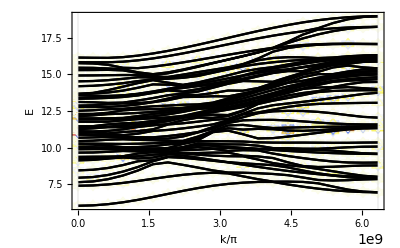
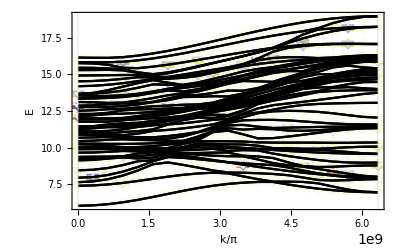
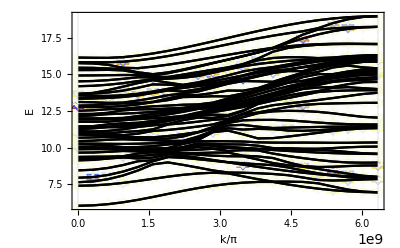
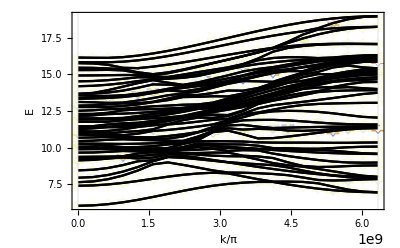
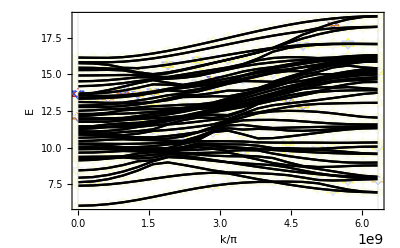

```mathematica
Table[WBandsplit[H1,syL[i],{{0,0},{0,2 Pi/a0}},20],{i,5}]
```

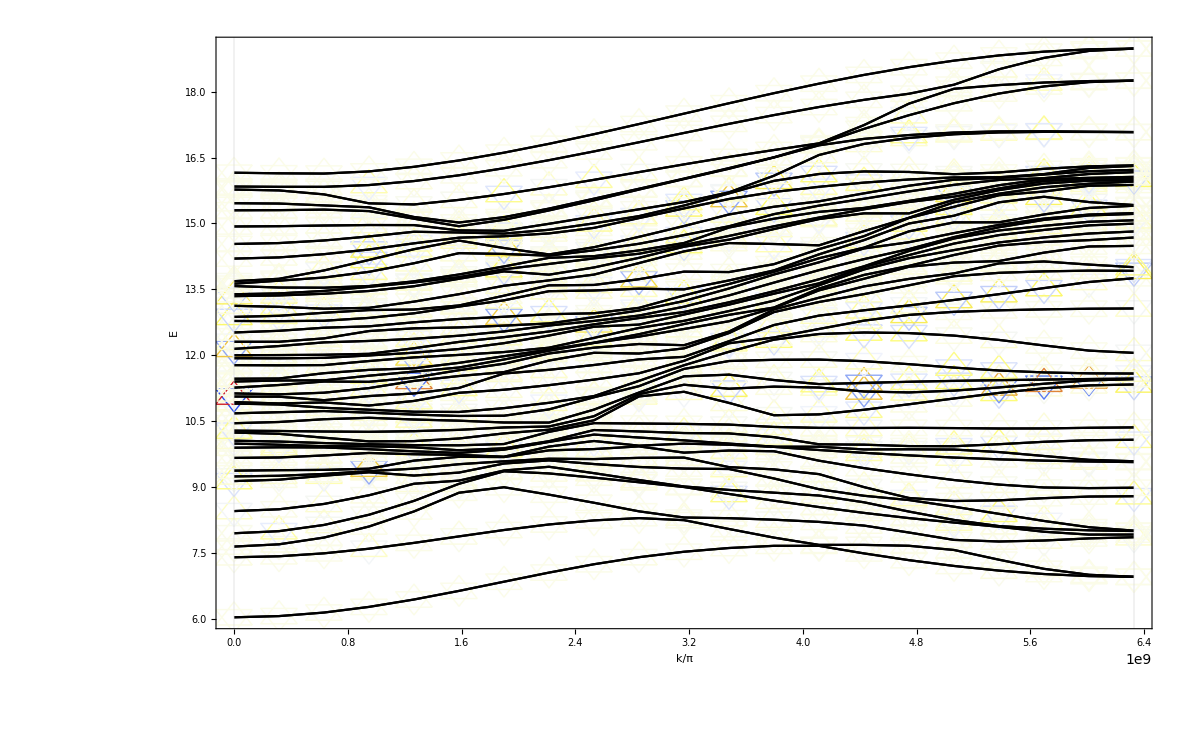

Required variables : , , kxky.

3 Segments
, , 0.6.32911×10^91.26582×10^10

Min = -0.996, Max = 0.996

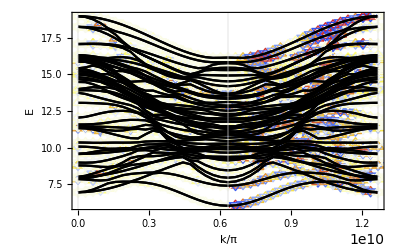

```mathematica
WBandsplit[H1,prsy,{{0,2 Pi/a0},{0,0},{2 Pi/a0,0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.864

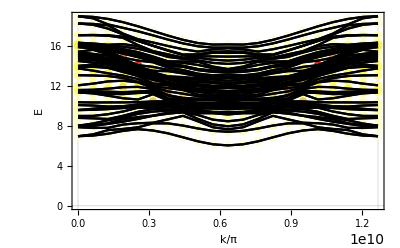

```mathematica
WBands[H1,pr[1],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.455

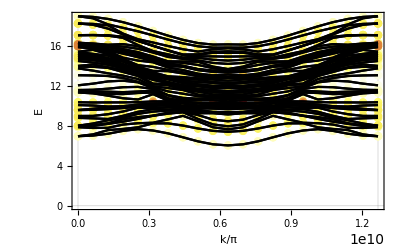

```mathematica
WBands[H1,pr[2],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.289

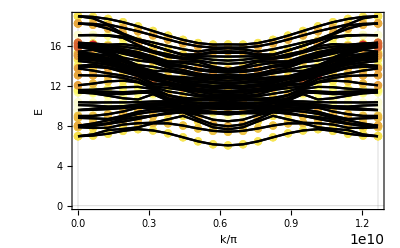

```mathematica
WBands[H1,pr[3],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.356

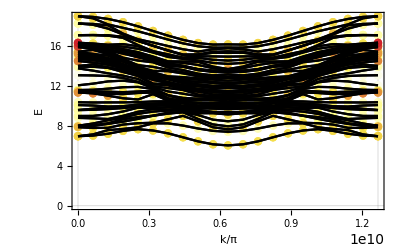

```mathematica
WBands[H1,pr[4],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.362

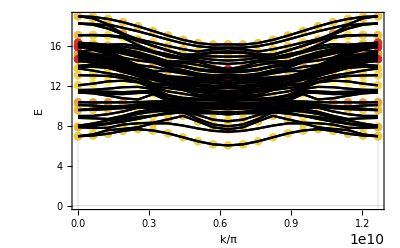

```mathematica
WBands[H1,pr[5],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

```mathematica
WBands[H1,pr[9],{{0,-2 Pi/a0},{0,2 Pi/a0}}]
```

Required variables : , , kxky.

2 Segments
, , 0.1.26582×10^10

Max = 0.864

-Graphics-